## H_5^+ DVR Adiabatic

Adiabatic treatment of H5+

## Average Field (Adiabatic Treatment)

### Load Package

```mathematica
Get@"~/Documents/UW/Research/H5+/Common/H5Core.m"
<<ChemTools`DVR`
<<ChemTools`Wavefunctions`
<<ChemTools`DataStructures`
<<ChemTools`Spectroscopy`
```

### Common

```mathematica
saMainGrid=$H5DVR["Grid"];
saGrid=saMainGrid["Points"];
```

```mathematica
h2SAPot//Clear
h2SAPot[{a_, s_}]:=
If[
With[{R1R2=RotationMatrix[-π/4].{a, s}, bounds=H5FullInterpPot[[1, 3]]},
AllTrue[R1R2, bounds[[1]]<=#<bounds[[2]]&]
],
h5PotCutVec[{a, s, Automatic, Automatic}],
$Failed
]
```

#### SA Stuff

This is misnamed as it’s really an (a,s) grid...but no energy to fix it.

```mathematica
saMainGrid=$H5DVR["Grid"];
saGrid=saMainGrid["Points"];
```

```mathematica
(*$h2SAPotMins=Import["~/Documents/UW/Research/H5+/inputs/sa_pot_mins.mx"];
h2SAPotMin[{a_, s_}]:=
h2SAPotMin[{a, s}]=
If[
With[{R1R2=RotationMatrix[-π/4].{a, s}, bounds=H5FullInterpPot[[1, 3]]},
AllTrue[R1R2, bounds[[1]]<=#<bounds[[2]]&]
],
NMinimize[
Evaluate[h5PotCut[{a, s, Automatic, Automatic}][{r1, r2}]],
{r1, r2}∈Rectangle[{.1, .1}, {2, 2}]
],
$Failed
]*)
```

```mathematica
(*potGridFunc=
 Module[
{
arr=QuantityMagnitude@H5Core`Private`H5FullPotQA,
gg
},
gg=
GatherBy[
arr, 
With[{p=#}, Round[#[[p]], .0001]&]&/@Range[3]
];
ChemTools`DataStructures`GridFunctionObject[
gg[[All, All, All, All, ;;4]],
#-Min[#]&@gg[[All, All, All, All, 5]]
]
];*)
```

```mathematica
(*Manipulate[
test=
potGridFunc@
"Compile"[{rr[[1]], rr[[2]], Automatic, Automatic},
"CoordinateTransformation"->
(Join[#[[;;2]], RotationMatrix[π/4.].#[[{4, 3}]]]&),
"Default"->10.^5
];
Join[
saGrid,
Transpose@List@test@saGrid,
2
]//ListPlot3D,
{rr, {.26, .26}, {1.8, 1.8}}
]*)
```

```mathematica
h2SAPot//Clear
h2SAPot[{a_, s_}]:=
If[
With[{R1R2=RotationMatrix[-π/4].{a, s}, bounds=H5FullInterpPot[[1, 3]]},
AllTrue[R1R2, bounds[[1]]<=#<bounds[[2]]&]
],
h5PotCutVec[{a, s, Automatic, Automatic}],
$Failed
]
```

```mathematica
h2SAPotSingles//Clear
h2SAPotSingles[{a_, s_}]:=
If[
With[{R1R2=RotationMatrix[-π/4].{a, s}, bounds=H5FullInterpPot[[1, 3]]},
AllTrue[R1R2, bounds[[1]]<=#<bounds[[2]]&]
],
h5PotCut[{a, s, Automatic, Automatic}],
$Failed
]
```

```mathematica
(*Quiet@
NMinimize[
H5FullInterpPot[r1, r2, R1, R2], 
{r1, r2, R1, R2}∈Region@Apply[Cuboid, Transpose@H5FullInterpPot[[1]]]
]*)
```

```mathematica
h2SAPotsGrid=
Flatten[
CoordinateBoundsArray[
H5FullInterpPot[[1, ;;2]],
(H5FullInterpPot[[1,1, 2]]-H5FullInterpPot[[1,1, 1]])/150
],
1
];
h2SAPotsUncoupled//Clear
h2SAPotsUncoupled[{a_, s_}]:=
h2SAPotsUncoupled[{a, s}]=
Module[
{
pot=h2SAPot[{a, s}](*h2SAPotSingles[{a, s}]*),
nmins,
r1,
r2,
vecs
},
If[pot=!=$Failed,
nmins=(* If this sucks too much just make a super refined grid over these points and use the vectorized version of the potential. That should be close-ish to right and a hell of a lot faster.
*)
MinimalBy[Thread[{h2SAPotsGrid, pot@h2SAPotsGrid}], Last][[1, 1]];
(*r1=$r1/.nmins;
r2=$r2/.nmins;*)
{r1, r2}=nmins;
{
Function[{gridList}, p[List/@gridList]]/.p->h5PotCutVec[{a, s, r1, Automatic}],
Function[{gridList}, p[List/@gridList]]/.p->h5PotCutVec[{a, s, Automatic, r2}]
},
$Failed
]
]
```

```mathematica
h2SAUncPots=AssociationMap[h2SAPotsUncoupled, saGrid];
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/h2_outer_SA_pots_uncoupled.mx", h2SAUncPots]*)
```

~/Documents/UW/Research/H5+/results/h2_outer_SA_pots_uncoupled.mx

```mathematica
h2SAUncPots=Import@"~/Documents/UW/Research/H5+/results/h2_outer_SA_pots_uncoupled.mx";
```

```mathematica
h2SAEqPts=
Nearest[
saGrid->"Index",
{0,2.1364750560940324}
]
h2SAEqPt=h2SAEqPts[[1]];
```

{1759,1819}

#### SA Grid

```mathematica
h2SAGrid=
$H2DVR[
"Grid",
 "PotentialOptimizationOptions"->{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->25
}
];
```

### H2 Coupled Treatment

#### H2 Wavefunctions

Get H_2 wavefunctions parametrized by (s, a)

```mathematica
(*h2SAWavefunctions=
AssociationMap[
With[{pot=h2SAPot[#]},
If[pot=!=$Failed,
$H2DVR[
"Wavefunctions",
 "PotentialEnergy"->SparseArray[Band[{1, 1}]->pot@h2SAGrid["Points"]],
"Grid"->h2SAGrid,
"ArnoldiIterations"->5000
],
$Failed
]
]&,
saGrid
];*)
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns_2.mx", h2SAWavefunctions]*)
```

~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns_2.mx

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns.mx", h2SAWavefunctions]*)
```

~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns.mx

```mathematica
h2SAWavefunctions=Import@"~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns_2.mx";
```

```mathematica
h2SAValidCoords=
Complement[
Range[Length@h2SAWavefunctions],
Pick[Range[Length@h2SAWavefunctions], Values[h2SAWavefunctions], $Failed]
];
```

```mathematica
h2SAInterestingWavefunctions=
Select[h2SAWavefunctions, #=!=$Failed&];
```

#### H2 Wavefunction Analysis

```mathematica
h2SAInterestingWavefunctions//Length
```

1740

```mathematica
h2Adiabats=
KeyValueMap[
If[#2===$Failed, 
Join[ConstantArray[#, 6], ConstantArray[{10.^9}, 6], 2], Join[ConstantArray[#, 6], List/@#2[[1, ;;6]], 2]]&,
h2SAWavefunctions
]//Transpose;
```

```mathematica
h2AdiabatInterps=Interpolation/@h2Adiabats;
```

Plot adiabats

```mathematica
h2Adiabats[[{2}]]
```

```mathematica
MinimalBy[h2Adiabats[[2]], Last, 2]
```

{{0.3484,1.57391,5871.65},{-0.3484,1.57391,5871.65}}

```mathematica
MinimalBy[h2Adiabats[[3]], Last, 2]
```

{{0.270978,1.57391,6003.91},{-0.270978,1.57391,6003.91}}

```mathematica
h2Adiabats[[{2}]]//ListPlot3D[Map[Select[#[[-1]]<10^8&], #], PlotRange->{{-1, 1}, {1, 3}, {0, 20000}+2000*{1, 1}}, InterpolationOrder->2, ClippingStyle->None, Boxed->False, AxesEdge->{{1,-1},{1,-1},{1,1}},
AxesLabel->Thread@Style[{"a (Å)", "s (Å)", "V (Å)"}, Black],
AxesStyle->Black
]&
```

-Graphics3D-

Plot differences

```mathematica
diffAds=
Module[
{
gps=Pick[h2Adiabats[[1, All, ;;2]], UnitStep[Abs[h2Adiabats[[1, All, 3]]]-10^8], 0],
ad0=Pick[#, UnitStep[Abs[#]-10^8], 0]&@h2Adiabats[[1, All, 3]],
ad1=Pick[#, UnitStep[Abs[#]-10^8], 0]&@h2Adiabats[[2, All, 3]],
ad2=Pick[#, UnitStep[Abs[#]-10^8], 0]&@h2Adiabats[[3, All, 3]],
mad0,
mad1,
mad2
},
mad0=Min@ad0;
mad1=Min@ad1;
mad2=Min@ad2;
ad0-=mad0;
ad1-=mad1;
ad2-=mad2;
Join[gps, List/@#, 2]&/@{ad1-ad0, ad2-ad0}
];
```

```mathematica
rf2=RegionMember@RegionResize[h5Reg, Scaled[.85]];
```

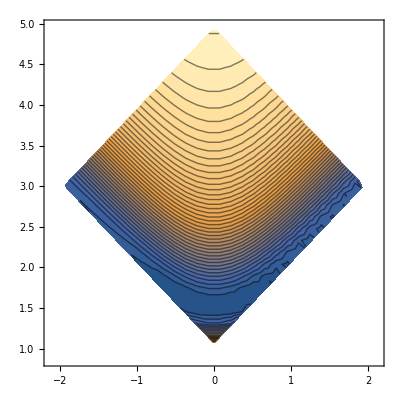

```mathematica
ListContourPlot[h2Adiabats[[1]],
 RegionFunction->({x, y}↦rf2[{x, y}]), Contours->50,
ColorFunction->"M10DefaultDensityGradient",
PlotRange->CoordinateBounds@Select[h2Adiabats[[1]], Abs[#[[3]]]<10^8&],
ContourLabels->None
]
```

```mathematica
rf3=RegionMember@RegionIntersection[RegionResize[h5Reg, Scaled[.85]], Rectangle[{-1, 1.4}, {1, 2}]];
```

```mathematica
ListPointPlot3D[h2Adiabats[[1]],
 RegionFunction->({x, y}↦rf3[{x, y}]),
ColorFunction->"M10DefaultDensityGradient",
PlotRange->CoordinateBounds@Select[h2Adiabats[[1]], rf3@#[[;;2]]&]
]
```

-Graphics3D-

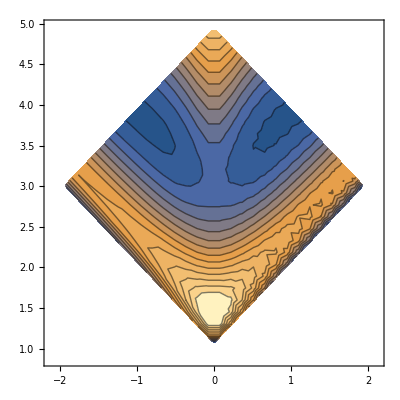

```mathematica
ListContourPlot[diffAds[[1]],
 RegionFunction->({x, y}↦rf2[{x, y}]), Contours->25,
ColorFunction->"M10DefaultDensityGradient",
ContourLabels->None
]
```

```mathematica
216/2
```

108

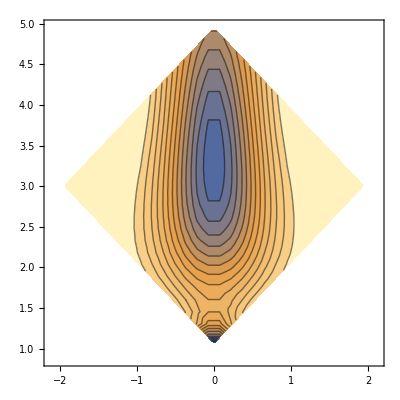

```mathematica
ListContourPlot[diffAds[[2]],
 RegionFunction->({x, y}↦rf2[{x, y}]), 
Contours->25,
ColorFunction->"M10DefaultDensityGradient",
ContourLabels->None
]
```

```mathematica
h2SAInterestingWavefunctions[[All, 1]]
```

Plot (some of) these suckers

```mathematica
Nearest[
Keys[h2SAInterestingWavefunctions]->"Index",
{0,2.1364750560940324}
]
```

{166,192}

```mathematica
h2SAInterestingWavefunctions[[{195}, 2, 2]]//MinMax
```

{-0.209289,0.206249}

```mathematica
Block[{(*ListDensityPlot=Echo*)},
KeyValueMap[
$H2DVR[
 "Wavefunctions"->#2,
"ShowPotential"->False,
"Grid"->Reverse[Reverse[h2SAGrid], {2}],
"PlotDisplayMode"->List,
"WavefunctionSelection"->5,
"PlotMode"->"Density",
"WavefunctionClipping"->None,
"WavefunctionRescaling"->None,
"WavefunctionScaling"->None,
"WavefunctionShifting"->None,
"ColorFunction"->"Rainbow",
"ColorFunctionScaling"->True,
FrameTicks->False(*,
PlotLabel->StringRiffle[#, ", "]*)
]&,
h2SAInterestingWavefunctions[[{1, 166, 391}]]
]
]//Iconize[#, "outer_wfns"]&
```

```mathematica
//ByteCount
```

#### H2 Distances

```mathematica
(*h2AveragedH2s=
If[#=!=$Failed,
$H2DVR[
"ExpectationValues",
#&,
"Grid"->h2SAGrid,
"Wavefunctions"->#,
"WavefunctionSelection"->50
],
$Failed
]&/@h2SAWavefunctions;*)
```

```mathematica
h2AveragedH2s=
Import["~/Documents/UW/Research/H5+/results/SA_grid_h2_dists.mx"];
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/SA_grid_h2_dists.mx", h2AveragedH2s]*)
```

~/Documents/UW/Research/H5+/SA_grid_h2_dists.mx

```mathematica
h2SAH2Dists=
Range[
Length@h2AveragedH2s[[h2SAEqPt]]]->
Thread[
Subtract@@@h2AveragedH2s[[h2SAEqPt, All, {1,2}]]//Thread
]//Thread//Association//SortBy[Abs@*Apply[Subtract]];
```

```mathematica
h2SAH2DistOrdering=
With[{n=Length@h2AveragedH2s[[h2SAEqPt]]},
Range[n]->
Thread[
With[{r=#},
Ordering@h2AveragedH2s[[h2SAEqPt, All, r]]->Range[n]//Thread//SortBy[#, First]&//Values
]&/@Range[2]
]//Thread//Association//SortBy[Abs@*Apply[Subtract]]
];
```

```mathematica
h2SAH2MeanDistOrdering=
With[{n=Length@h2AveragedH2s[[h2SAEqPt]]},
Range[n]->
Thread[
With[{r=#},
Ordering@
Mean@Select[h2AveragedH2s, #=!=$Failed&][[All, All, r]]->Range[n]//Thread//SortBy[#, First]&//Values
]&/@Range[2]
]//Thread//Association//SortBy[Abs@*Apply[Subtract]]
];
```

#### Analysis

##### Overlaps

```mathematica
h2OverlapMatrix[i_, j_]:=
Module[
{
wooplen=Length@h2SAInterestingWavefunctions[[1, 2, 1]],
woopart1,
woopart2,
flooplen=Length@h2SAWavefunctions
},
woopart1=
Map[
If[#===$Failed, ConstantArray[0., wooplen], #[[2, i]]]&,
Values@h2SAWavefunctions
];
woopart2=
Map[
If[#===$Failed, ConstantArray[0., wooplen], #[[2, j]]]&,
Values@h2SAWavefunctions
];
h2OverlapMatrix[i, j]=
SparseArray@$H2DVR["OperatorMatrix",
(#2&),
"Wavefunctions"->{ConstantArray[0, 2*flooplen], Join[woopart1,woopart2]}
]
]
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_1_2.mx",
h2OverlapMatrix[1, 2]
]
```

~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_1_2.mx

```mathematica
"~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_2_3.mx"//Import//MatrixPlot
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_2_3.mx",
h2OverlapMatrix[2, 3]
]
```

```mathematica
h2OverlapMatrix[2, 3]=Import["~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_2_3.mx"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_1_3.mx",
h2OverlapMatrix[1, 3]
]
```

$Aborted

```mathematica
h2OverlapMatrix[2, 3]//Image
```

##### Coupled KE

```mathematica
h2CoupledKineticEnergy[i_, j_]:=
Module[
{
woop=h2OverlapMatrix[i, j],
waap=$H5DVR["KineticEnergy"],
klap,
leeen
},
leeen=Length@waap;
(*woop=
Join[
Join[IdentityMatrix[leeen, SparseArray],woop[[;;leeen, leeen+1;;]], 2],
Join[woop[[leeen+1;;, ;;leeen]],IdentityMatrix[leeen, SparseArray], 2]
];*)
klap=
Join[
Join[waap,waap, 2],
Join[waap,waap, 2]
];
woop*klap
];
```

```mathematica
ke=h2CoupledKineticEnergy[2, 3];
```

##### Pots

```mathematica
h2AveragedEnergy[i_]:=
Map[
If[#===$Failed, 10^9//N, #[[1, i]]]&,
Values@h2SAWavefunctions
];
```

##### Hammer

```mathematica
h5AdiabatCoupledHam[i_, j_]:=
Module[
{
h1=
$H5DVR["Hamiltonian",
 "PotentialEnergy"->SparseArray[Band[{1, 1}]->h2AveragedEnergy[i]]
],
h2=
$H5DVR["Hamiltonian",
 "PotentialEnergy"->SparseArray[Band[{1, 1}]->h2AveragedEnergy[j]]
],
kt=h2CoupledKineticEnergy[i, j]
},
SparseArray[Band[{1, 1}]->Join[h2AveragedEnergy[i], h2AveragedEnergy[j]]]+kt
]
```

```mathematica
Export["~/Documents/UW/Research/H5+/results/h5AdiabatCoupledHam_2_3.mx", h5AdiabatCoupledHam[2, 3]]
```

~/Documents/UW/Research/H5+/results/h5AdiabatCoupledHam_2_3.mx

```mathematica
h5TwoStateHam=h5AdiabatCoupledHam[2, 3];
```

```mathematica
h5TwoStateHam//MatrixPlot
```

-Graphics-

```mathematica
h5TwoStateEnergies=
$H5DVR["Energies",
"KineticEnergy"->h5TwoStateHam,
"PotentialEnergy"->N@SparseArray[{}, Dimensions@h5TwoStateHam],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000
];//AbsoluteTiming//First
```

30.4747

```mathematica
Rest[#]-#[[1]]&@h5TwoStateEnergies
```

{26.8045,464.369,484.983,788.464,808.543,1138.03,1154.8,1377.13,1394.65,1674.99,1685.12,1779.02,1796.02,1981.21,1995.08,2131.25,2139.6,2315.21,2323.98,2477.75,2482.07,2616.83,2621.54,2733.6,2734.1,2808.36,2822.25,2878.77,2879.58,2945.44,2948.22,3064.3,3068.32,3153.17,3154.81,3276.75,3278.05,3400.56,3404.44,3519.84,3522.35,3626.99,3634.4,3691.01,3703.42,3793.16,3795.74,3914.32,3916.4,4074.52,4081.63,4217.02,4219.85,4253.61,4270.15,4345.6,4349.1,4402.35,4410.38,4577.97,4583.03,4689.34,4689.84,4790.82,4803.98,4882.67,4893.53,4994.04,4997.42,5120.07,5122.53,5231.15,5240.08,5280.71,5291.84,5354.62,5359.65,5402.99,5410.47,5524.58,5525.03,5582.41,5592.43,5638.23,5642.7,5697.23,5700.8,5835.77,5839.84,5903.54,5903.78,5972.24,5972.85,6033.83,6034.82,6113.36,6117.04,6206.29,6211.05}

```mathematica
Iconize[h5TwoStateEnergies, "Coupled 1,0/0,1 Energies"]
```

Want to look at wavefunctions too, probably:

```mathematica
h5TwoStateWavefunctions=
$H5DVR["GridWavefunctions",
"Grid"->Join[$H5DVR["Grid"], $H5DVR["Grid"]],
"KineticEnergy"->h5TwoStateHam,
"PotentialEnergy"->N@SparseArray[{}, Dimensions@h5TwoStateHam],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000
];//AbsoluteTiming//First
```

30.9101

```mathematica
Table[
{h5TwoStateWavefunctions[[n, 3601;;]], h5TwoStateWavefunctions[[n, ;;3600]]}//Map[ListPlot3D[#, PlotRange->All, ColorFunction->"Rainbow", ImageSize->250]&],
{n, 6}
]//Grid
```

##### 1,2 Coupling

```mathematica
ham12=h5AdiabatCoupledHam[1, 2];
```

```mathematica
schloopWavefunctions2=
$H5DVR["GridWavefunctions",
"Grid"->Join[$H5DVR["Grid"], $H5DVR["Grid"]],
"KineticEnergy"->ham12,
"PotentialEnergy"->N@SparseArray[{}, Dimensions@ham12],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000
];//AbsoluteTiming//First
```

27.4752

```mathematica
With[{n=1},
{schloopWavefunctions2[[n, 3601;;]], schloopWavefunctions2[[n, ;;3600]]}//Map[ListPlot3D[#, PlotRange->All, ColorFunction->"Rainbow"]&]
]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
With[{n=2},
{schloopWavefunctions2[[n, 3601;;]], schloopWavefunctions2[[n, ;;3600]]}//Map[ListPlot3D[#, PlotRange->All, ColorFunction->"Rainbow"]&]
]
```

{-Graphics3D-,-Graphics3D-}

##### 1,3 Coupling

```mathematica
ham13=h5AdiabatCoupledHam[1, 3];
```

```mathematica
schloopWavefunctions3=
$H5DVR["GridWavefunctions",
"Grid"->Join[$H5DVR["Grid"], $H5DVR["Grid"]],
"KineticEnergy"->ham13,
"PotentialEnergy"->N@SparseArray[{}, Dimensions@ham13],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000
];//AbsoluteTiming//First
```

29.3996

```mathematica
With[{n=1},
{schloopWavefunctions3[[n, 3601;;]], schloopWavefunctions3[[n, ;;3600]]}//Map[ListPlot3D[#, PlotRange->All, ColorFunction->"Rainbow"]&]
]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
With[{n=2},
{schloopWavefunctions3[[n, 3601;;]], schloopWavefunctions3[[n, ;;3600]]}//Map[ListPlot3D[#, PlotRange->All, ColorFunction->"Rainbow"]&]
]
```

{-Graphics3D-,-Graphics3D-}

##### Old Engs

This was from a ground-state coupled to first excited state

```mathematica
oldEngs=;
```

```mathematica
oldEngs[[2]]-oldEngs[[2, 1]]
```

{0.,441.295,766.866,1107.64,1350.34,1645.77,1730.08,1935.05,2082.75,2271.5,2431.68,2563.65,2649.79,2743.64,2774.72,2925.6,2954.39,3105.24,3195.35,3329.94,3382.84,3463.73,3474.2,3568.49,3668.65,3788.12,3837.85,4004.99,4089.69,4114.17,4124.45,4255.8,4273.18,4428.16,4493.41,4563.55,4617.63,4697.94,4738.23,4899.54,4935.43,4943.74,5051.56,5057.7,5135.09,5233.42,5266.27,5303.95,5324.14,5379.5,5445.39,5497.95,5527.13,5551.1,5653.06,5671.16,5753.87,5808.,5832.86,5886.74,5940.6,5987.12,6045.79,6069.96,6088.09,6159.13,6186.04,6226.35,6228.84,6337.92,6342.58,6403.79,6497.08,6498.44,6525.51,6560.13,6617.4,6719.48,6757.26,6760.04,6793.55,6819.19,6922.88,6935.47,6987.48,6992.33,7021.63,7056.53,7159.46,7254.35,7291.83,7336.28,7371.56,7425.,7451.22,7469.37,7525.92,7541.15,7642.45,7708.76}

Old run with the coupled states

```mathematica
schloop2=h5AdiabatCoupledHam[2, 3];
```

```mathematica
$H5DVR["Energies",
"KineticEnergy"->schloop2,
"PotentialEnergy"->N@SparseArray[{}, Dimensions@schloop2],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000
]//AbsoluteTiming
```

{31.6139,{6944.02,6970.83,7408.39,7429.01,7732.49,7752.56,8082.05,8098.82,8321.15,8338.67,8619.01,8629.14,8723.05,8740.04,8925.23,8939.1,9075.28,9083.62,9259.24,9268.,9421.77,9426.09,9560.85,9565.56,9677.62,9678.12,9752.38,9766.27,9822.79,9823.6,9889.46,9892.24,10008.3,10012.3,10097.2,10098.8,10220.8,10222.1,10344.6,10348.5,10463.9,10466.4,10571.,10578.4,10635.,10647.4,10737.2,10739.8,10858.3,10860.4,11018.5,11025.7,11161.,11163.9,11197.6,11214.2,11289.6,11293.1,11346.4,11354.4,11522.,11527.1,11633.4,11633.9,11734.8,11748.,11826.7,11837.6,11938.1,11941.4,12064.1,12066.5,12175.2,12184.1,12224.7,12235.9,12298.6,12303.7,12347.,12354.5,12468.6,12469.1,12526.4,12536.5,12582.3,12586.7,12641.3,12644.8,12779.8,12783.9,12847.6,12847.8,12916.3,12916.9,12977.9,12978.8,13057.4,13061.1,13150.3,13155.1}}

```mathematica
%235[[2]]-%235[[2, 1]]
```

{0.,26.8045,464.369,484.983,788.464,808.543,1138.03,1154.8,1377.13,1394.65,1674.99,1685.12,1779.02,1796.02,1981.21,1995.08,2131.25,2139.6,2315.21,2323.98,2477.75,2482.07,2616.83,2621.54,2733.6,2734.1,2808.36,2822.25,2878.77,2879.58,2945.44,2948.22,3064.3,3068.32,3153.17,3154.81,3276.75,3278.05,3400.56,3404.44,3519.84,3522.35,3626.99,3634.4,3691.01,3703.42,3793.16,3795.74,3914.32,3916.4,4074.52,4081.63,4217.02,4219.85,4253.61,4270.15,4345.6,4349.1,4402.35,4410.38,4577.97,4583.03,4689.34,4689.84,4790.82,4803.98,4882.67,4893.53,4994.04,4997.42,5120.07,5122.53,5231.15,5240.08,5280.71,5291.84,5354.62,5359.65,5402.99,5410.47,5524.58,5525.03,5582.41,5592.43,5638.23,5642.7,5697.23,5700.8,5835.77,5839.84,5903.54,5903.78,5972.24,5972.85,6033.83,6034.82,6113.36,6117.04,6206.29,6211.05}

### H2 Uncoupled Treatment

```mathematica
h2SAWavefunctions=
Import@"~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns_2.mx";
```

```mathematica
h2SAWavefunctions=
Import@"~/Documents/UW/Research/H5+/results/h2SAWavefunctions_2.mx";
```

#### Phase Corrections

```mathematica
rephaseThingies=
Compile[{{overlaps, _Real, 1}, {init, _Integer}, {tol, _Real}},
Module[{prev, el, ov=overlaps,swapEl=init},
Prepend[
Table[
el=ov[[i]];
If[el<-tol, swapEl=-swapEl];
swapEl,
{i, Length@ov}
],
init
]
](*,
CompilationTarget->"C"*)
];
rephaseWfns[s_, wfns_]:=
WavefunctionsObject[
{
wfns["Energies"], 
Map[Scale[#, s]&, wfns["Wavefunctions"]]
},
wfns["Grid"]
]
getPhaseCorrection//Clear
getPhaseCorrection[wfs_List, 
grid_,
state:{_Integer?IntegerQ}:{2},
 basePhase:1|-1:1,
rephase:True|False:False
]:=
Module[
{
pos,
gridPoints=grid["Points"],
cleanGrid,
cleanGridSorted,
gridReordering,
gridPositions,
reorderedWfs,
rephasedWavefunctions,
fullWfs,
overlaps,
phases,
orderComplement,
phaseVector,
newWfns
},
pos=Select[IntegerQ[#]&&#>0&]@Flatten@Position[wfs, _WavefunctionsObject, {1}];
cleanGrid=Round[grid[[pos]].RotationMatrix[π/4], .001];
cleanGridSorted=
MapIndexed[If[EvenQ[#2[[1]]], Reverse, Identity]@#&]@
SortBy[
SortBy[#, First]&/@GatherBy[cleanGrid, -#[[-1]]&], 
-#[[1, -1]]&
];
gridReordering=
Flatten@
Lookup[PositionIndex[cleanGrid], Flatten[cleanGridSorted, 1]
];
gridPositions=pos[[gridReordering]];
reorderedWfs=wfs[[gridPositions]];
fullWfs=
WavefunctionsObject[
Flatten/@
Transpose[
{#["Energies"], #["Wavefunctions"][[state]]}&/@
reorderedWfs
],
reorderedWfs[[1]]["Grid"]
];
overlaps=Developer`ToPackedArray[fullWfs@"Overlaps"[fullWfs]];
phases=rephaseThingies[Diagonal[overlaps, 1], basePhase, 0];
orderComplement=Complement[Range[Length@wfs], gridPositions];
phaseVector=
Join[phases, ConstantArray[$Failed, Length@orderComplement]][[
Ordering@Join[gridPositions, orderComplement]
]];
If[rephase,
newWfns=
MapThread[
If[#===$Failed,
#,
rephaseWfns[#, #2] 
]&,
{
phaseVector,
wfs
}
],
newWfns=None
];
<|
"Wavefunctions"->newWfns,
"PhaseVector"->phaseVector,
"Positions"->pos,
"Ordering"->gridPositions,
"Phases"->phases
|>
];
getPhaseCorrection[wfs_List, 
grid_,
states:{_Integer?IntegerQ, __Integer?IntegerQ},
 basePhase:1|-1:1,
rephase:True|False:True
]:=
Module[{wfSets, rephasing, newWfns},
wfSets=Table[If[#===$Failed, #, #[[{state}]]]&/@wfs, {state, states}];
rephasing=
Map[getPhaseCorrection[#, grid, {1}, basePhase, False]&, wfSets ];
If[rephase,
newWfns=
MapThread[
If[#===$Failed, #, Join[##]]&,
MapThread[
MapThread[
If[#===$Failed,
#,
rephaseWfns[#, #2] 
]&,
{
#["PhaseVector"],
#2
}
]&,
{rephasing, wfSets}
]
],
newWfns=None
];
<|
"Wavefunctions"->newWfns,
"Rephasings"->rephasing
|>
]
getVectorPhaseCorrection//Clear
getVectorPhaseCorrection[values_List, 
grid_, 
basePhase:1|-1:1,
rephase:True|False:True,
tol:_Real:.001
]:=
Module[
{
pos,
gridPoints=grid["Points"],
cleanGrid,
cleanGridSorted,
gridReordering,
gridPositions,
ratios,
reorderedVals,
phases,
orderComplement,
phaseVector,
newValues
},
pos=Flatten@Position[values, _?NumericQ, {1}];
cleanGrid=Round[grid[[pos]].RotationMatrix[π/4], .001];
cleanGridSorted=
MapIndexed[If[EvenQ[#2[[1]]], Reverse, Identity]@#&]@
SortBy[
SortBy[#, First]&/@GatherBy[cleanGrid, -#[[-1]]&], 
-#[[1, -1]]&
];
gridReordering=
Flatten@
Lookup[PositionIndex[cleanGrid], Flatten[cleanGridSorted, 1]
];
gridPositions=pos[[gridReordering]];
reorderedVals=values[[gridPositions]];
ratios=MovingMap[If[#[[2]]≠0, Divide@@#, 0.]&, reorderedVals(*Differences[reorderedVals]*), 1];
(*AppendTo[ratios, ratios[[-1]]]; *)
phases=rephaseThingies[ratios, basePhase, tol];
orderComplement=Complement[Range[Length@values], gridPositions];
phaseVector=
Join[phases, ConstantArray[$Failed, Length@orderComplement]][[
Ordering@Join[gridPositions, orderComplement]
]];
If[rephase,
newValues=
values*Replace[phaseVector, $Failed->1, 1],
newValues=None
];
<|
"Values"->newValues,
"PhaseVector"->phaseVector,
"Positions"->pos,
"Ordering"->gridPositions,
"Phases"->phases
|>
]
```

#### SCF Procedure

```mathematica
scfCoeffs=Import@"~/Documents/UW/Research/H5+/results/scf_coeffs.mx";
```

##### SCF Wavefunction Computation

```mathematica
h2SCFGrid=
$H2DVR["Grid",
"Points"->{60, 60},
"PotentialOptimize"->False
];
```

```mathematica
h2SAPlotTexture[pot_CompiledFunction]:=
Module[
{
zerp
},
zerp=h2SCFGrid@"BuildFunction"[pot[{#}][[1]]&];
zerp@"Plot"["PlotMode"->"Contour", Axes->False, Frame->False, ImagePadding->None, PlotRangePadding->None]
];
h2SAPlotTexture[{a_, s_}]:=
h2SAPlotTexture@h2SAPot@{a, s}
```

```mathematica
h2SCFWavefunction//Clear
h2SCFWavefunction[
pot_CompiledFunction,
states:{{_Integer, _Integer}..},
n:_Integer|Automatic:Automatic
]:=
WavefunctionsObject[
"SCF",
$H2SingleDVR,
GridFunctionObject[
h2SCFGrid,
pot@h2SCFGrid["Points"]
],
"StateVectors"->states,
"MaxIterations"->n
];
h2SCFWavefunction[
{a_, s_},
states:{{_Integer, _Integer}..},
n:_Integer|Automatic:Automatic
]:=
Module[{pot=h2SAPot[{a, s}]},
If[pot===$Failed,
$Failed,
h2SCFWavefunction[
pot,
states,
n
]
]
];
h2SCFWavefunctionData//Clear
h2SCFWavefunctionData[
pot_CompiledFunction,
states:{{_Integer, _Integer}..},
its:_Integer|Automatic:Automatic
]:=
ChemTools`Wavefunctions`Package`SelfConsistentWavefunctions[
$H2SingleDVR,
GridFunctionObject[
h2SCFGrid,
pot@h2SCFGrid["Points"]
],
"StateVectors"->states,
"MaxIterations"->its
];
```

```mathematica
h2SCFCoeffData//Clear
h2SCFCoeffData[
{a_, s_}(*,
wfns:{__Integer}*)
]:=
Module[
{
pot=h2SAPot[{a, s}],
wfs,
wfs2D,
coeffs,
expand
},
If[pot===$Failed,
$Failed,
wfs=
h2SCFWavefunction[
pot,
{
{1, 1},
 {1, 2}, {2, 1}, 
{3, 1}, {2, 2}, {1, 3},
{4, 1}, {2, 3}, {3, 2}, {1, 4}
}
];
wfs2D=
$H2DVR[
"Points"->{60, 60},
"PotentialOptimize"->False,
"PotentialFunction"->pot,
"NumberOfWavefunctions"->10
]["Wavefunctions"];(*
coeffs=wfs2D[[{2, 3}]]@"Overlaps"[wfs];
expand=
Map[
Function[
#@"Add"[#2]&@@
MapThread[Scale,{wfs["Wavefunctions"],#}]
],
coeffs
];
expand=WavefunctionsObject[{wfs["Energies"], expand}, expand[[1]]["Grid"]];*)
<|(*
"Coefficients"->coeffs, *)
"SCFWavefunctions"->wfs, 
"DVRWavefunctions"->wfs2D(*,
"ExpansionWavefunctions"->expand*)
|>
]
]
```

```mathematica
cdata=h2SCFCoeffData[saGrid[[150]]];//AbsoluteTiming
```

```mathematica
cdataFull=h2SCFCoeffData/@saGrid;//AbsoluteTiming
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/coeffs_and_wfns3.mx", cdataFull2]*)
```

~/Documents/UW/Research/H5+/results/coeffs_and_wfns3.mx

```mathematica
coefficientData=Import@"~/Documents/UW/Research/H5+/results/coeffs_and_wfns3.mx";
```

##### Phases Attempt 2 (but doesn’t quite work)

```mathematica
realShit=Select[cdataFull2, AssociationQ];
```

```mathematica
ChemTools["Get", "Wavefunctions/Package/WavefunctionTools"]
```

```mathematica
ChemTools["Get", "Wavefunctions/WavefunctionsObject"]
```

```mathematica
scfShit=Join@@realShit[[All, "SCFWavefunctions"]];
scfWfs1=scfShit[[1;;;;2]];
scfWfs2=scfShit[[1;;;;2]];
```

```mathematica
ChemTools`Wavefunctions`Package`WFRephase//Options
```

{BasePhase→1,Reorder→False,Method→Automatic}

```mathematica
scfReph1=scfWfs1@"Rephase"["BasePhase"->-1];
scfReph2=scfWfs2@"Rephase"[];
```

```mathematica
dvrShit=Join@@realShit[[All, "DVRWavefunctions"]];
dvrWfs1=dvrShit[[1;;;;2]];
dvrWfs2=dvrShit[[2;;;;2]];
```

```mathematica
dvrReph1=dvrWfs1@"Rephase"[];
dvrReph2=dvrWfs2@"Rephase"[];
```

```mathematica
scfCoeffs1=
Transpose[{
Diagonal[dvrReph1@"Overlaps"[scfReph1]],
Diagonal[dvrReph1@"Overlaps"[scfReph2]]
}];
scfCoeffs2=
Transpose@{
Diagonal[dvrReph2@"Overlaps"[scfReph1]],
Diagonal[dvrReph2@"Overlaps"[scfReph2]]
};
```

```mathematica
scfCoeffs=
Join[scfCoeffs1, scfCoeffs2];
```

##### Phase Correction

The idea is that we want to take our initial DVR wavefunctions and make sure that they have a consistently positive overlap gridpoint to gridpoint scanning over the entire range (note not entirely positive, just pairwise positive).

Because this is all so fast we’ll do it in the least-buggy way which is to first take all our DVR wavefunctions and order them so they’re cleanly ordered on the R1/R2 grid. To do this we first extract the R1/R2 grid:

```mathematica
scfRealPos=Flatten@Position[coefficientData, _Association, {1}];
```

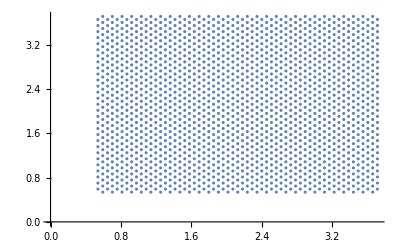

```mathematica
cleanGrid=Round[saGrid[[scfRealPos]].RotationMatrix[π/4], .001];
cleanGrid//ListPlot
```

Then we order it and unwrap so that we’re always making very small jumps from gridpoint to gridpoint:

```mathematica
cleanGridSorted=
MapIndexed[If[EvenQ[#2[[1]]], Reverse, Identity]@#&]@
SortBy[
SortBy[#, First]&/@GatherBy[cleanGrid, -#[[-1]]&], 
-#[[1, -1]]&
];
```

```mathematica
(*ListPlot[
MapIndexed[Style[#, GrayLevel[FractionalPart[#2[[1]]/(10)]]]&, Flatten[cleanGridSorted, 1]],
AspectRatio->1
]*)
```

Next we determine the ordering of the original grid that provided us with this next grid ordering and figure out how to select from the collected wavefunctions to obtain DVR wavefunctions in this order

```mathematica
gridReorderingY=
Flatten@
Lookup[PositionIndex[cleanGrid], Flatten[cleanGridSorted, 1]
];
gridPositionsRealY=scfRealPos[[gridReorderingY]];
```

Then we collect our DVR wavefunctions and overlap each of them with each other one:

```mathematica
fullDVRWfs1Y=
WavefunctionsObject[
Flatten/@
Transpose[
{#["Energies"], #["Wavefunctions"][[{1}]]}&/@
coefficientData[[gridPositionsRealY, "DVRWavefunctions"]]
],
coefficientData[[gridPositionsRealY[[1]], "DVRWavefunctions"]]["Grid"]
];
fullDVRWfs2Y=
WavefunctionsObject[
Flatten/@
Transpose[
{#["Energies"], #["Wavefunctions"][[{2}]]}&/@
coefficientData[[gridPositionsRealY, "DVRWavefunctions"]]
],
coefficientData[[gridPositionsRealY[[1]], "DVRWavefunctions"]]["Grid"]
];
dvrOverlaps1=
Developer`ToPackedArray[fullDVRWfs1Y@"Overlaps"[fullDVRWfs1Y]];
dvrOverlaps2=
Developer`ToPackedArray[fullDVRWfs2Y@"Overlaps"[fullDVRWfs2Y]];
```

Next we make use of the ordering that we had and note that the first subdiagonal of the overlap matrix will give every function with the one on the previous nearest gridpoint:

```mathematica
rephaseThingies=
Compile[{{overlaps, _Real, 1}, {init, _Integer}},
Module[{prev, el, ov=overlaps,swapEl=init},
Prepend[
Table[
el=ov[[i]];
If[el<0, swapEl=-swapEl];
swapEl,
{i, Length@ov}
],
init
]
],
CompilationTarget->"C"
];
```

```mathematica
dvrPhases1=rephaseThingies[Diagonal[dvrOverlaps1, 1], 1];
dvrPhases2=rephaseThingies[Diagonal[dvrOverlaps2, 1], 1];
```

Then we just multiply these phases into the DVR wavefunctions we have:

```mathematica
newDVRWfns1=
MapThread[If[#===-1, Scale[#2, -1], #2]&, {dvrPhases1, fullDVRWfs1Y["Wavefunctions"]}];
newDVRWfnsObj1=
WavefunctionsObject[
{
fullDVRWfs1Y["Energies"],
newDVRWfns1
},
newDVRWfns1[[1]]["Grid"]
];
newDVRWfns2=
MapThread[If[#===-1, Scale[#2, -1], #2]&, {dvrPhases2, fullDVRWfs2Y["Wavefunctions"]}];
newDVRWfnsObj2=
WavefunctionsObject[
{
fullDVRWfs2Y["Energies"],
newDVRWfns2
},
newDVRWfns2[[1]]["Grid"]
];
```

```mathematica
(*With[{n=13, d=60, s=6, c=60},
newDVRWfnsObj2[[(n-1)*c;;(n-1)*c+d;;s]]@"Plot"[ColorFunction->"ThermometerColors", ViewPoint->Above]
]*)
```

Now we take our SCF wavefunctions subject to the same ordering and ensure a consistent phase across them:

```mathematica
scfWfnsReordered1=
WavefunctionsObject[
Flatten/@
Transpose[
{#["Energies"], #["Wavefunctions"][[{1}]]}&/@
coefficientData[[gridPositionsRealY, "SCFWavefunctions"]]
],
coefficientData[[gridPositionsRealY[[1]], "SCFWavefunctions"]]["Grid"]
];
scfWfnsReordered2=
WavefunctionsObject[
Flatten/@
Transpose[
{#["Energies"], #["Wavefunctions"][[{2}]]}&/@
coefficientData[[gridPositionsRealY, "SCFWavefunctions"]]
],
coefficientData[[gridPositionsRealY[[1]], "SCFWavefunctions"]]["Grid"]
];
scfOverlaps1=
Developer`ToPackedArray[scfWfnsReordered1@"Overlaps"[scfWfnsReordered1]];
scfOverlaps2=
Developer`ToPackedArray[scfWfnsReordered2@"Overlaps"[scfWfnsReordered2]];
```

```mathematica
scfPhases1=rephaseThingies[Diagonal[scfOverlaps1, 1], -1];scfPhases2=rephaseThingies[Diagonal[scfOverlaps2, 1], 1];
```

```mathematica
newSCFWfns1=
MapThread[If[#===-1, Scale[#2, -1], #2]&, {scfPhases1, scfWfnsReordered1["Wavefunctions"]}];
newSCFWfnsObj1=
WavefunctionsObject[
{
scfWfnsReordered1["Energies"],
newSCFWfns1
},
newSCFWfns1[[1]]["Grid"]
];
newSCFWfns2=
MapThread[If[#===-1, Scale[#2, -1], #2]&, {scfPhases2, scfWfnsReordered2["Wavefunctions"]}];
newSCFWfnsObj2=
WavefunctionsObject[
{
scfWfnsReordered2["Energies"],
newSCFWfns2
},
newSCFWfns2[[1]]["Grid"]
];
```

Next we take overlaps of these with DVR wavefunctions to recover our expansion coefficients:

```mathematica
scfCoeffs1=
Transpose[{
Diagonal[newDVRWfnsObj1@"Overlaps"[newSCFWfnsObj1]],
Diagonal[newDVRWfnsObj1@"Overlaps"[newSCFWfnsObj2]]
}];
scfCoeffs2=
Transpose@{
Diagonal[newDVRWfnsObj2@"Overlaps"[newSCFWfnsObj1]],
Diagonal[newDVRWfnsObj2@"Overlaps"[newSCFWfnsObj2]]
};
```

Finally we put everything back in the original ordering for consistency’s sake:

```mathematica
scfCoeffs=
Join[
scfCoeffs1[[Ordering[gridPositionsRealY]]],
-scfCoeffs2[[Ordering[gridPositionsRealY]]]
];
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/scf_coeffs.mx", scfCoeffs]*)
```

~/Documents/UW/Research/H5+/results/scf_coeffs.mx

##### SCF for next packet

```mathematica
ChemTools["Get", "DataStructures/Package/GridTools"]
ChemTools["Get", "DataStructures/Package/GridFunctions"]
ChemTools["Get", "Wavefunctions/Package/WavefunctionTools"]
```

```mathematica
scfWavefunctions=Import@"~/Documents/UW/Research/H5+/results/coeffs_and_wfns4.mx";
```

```mathematica
overt=Import@"~/Documents/UW/Research/H5+/results/overlaps_456.mx";
```

```mathematica
rephasingData=
getPhaseCorrection[Values@h2SAWavefunctions, Keys[h2SAWavefunctions], Range[10]];
```

```mathematica
rephasedH2s2=
AssociationThread[
Keys[h2SAWavefunctions],
rephasingData["Wavefunctions"]
];
```

```mathematica
blerp=Select[rephasedH2s2, #=!=$Failed&];
```

```mathematica
ova1=
Join@@Join@@Table[Map[#[[{n}]]&, Values[blerp]], {n, 3}];
```

```mathematica
zoop=ova1@"Overlaps"[ova1];//AbsoluteTiming
```

{1.05725,Null}

```mathematica
overt=Developer`ToPackedArray@zoop;
```

```mathematica
fleng=Length[h2SAWavefunctions];
goodPlace=Pick[Range[Length@h2SAWavefunctions], Values[#=!=$Failed&/@h2SAWavefunctions]];
goodPos=Join@@Map[#+goodPlace&, {0, 1, 2}*fleng];
goodPairs=Developer`ToPackedArray@Tuples[goodPos, 2];
```

```mathematica
goodSparse456=SparseArray[goodPairs->Flatten@overt,3*fleng*{1,1} , 0.];(*
goodSparse=goodSparse-SparseArray[Band[{1, 1}]->Diagonal[goodSparse]];
goodSparse=goodSparse+IdentityMatrix[Length@goodSparse, SparseArray];*)
```

```mathematica
h2SCFOverlapMat=goodSparse456;
```

#### H2 Wavefunctions

##### Phase Correction

This builds off the SCF phase correction. When I include my GS stuff in the SCF calc I will no longer need this

```mathematica
fullH2SAWfs=
If[#=!=$Failed,
#@"CorrectPhase"[],
#
]&/@h2SAWavefunctions;
```

```mathematica
h2WFRealPos=
Flatten@Position[Values@h2SAWavefunctions, _WavefunctionsObject, {1}];
```

```mathematica
h2SAWfsFullObj=
Join@@Map[#[[{2}]]&, Values[fullH2SAWfs][[h2WFRealPos]]];
```

```mathematica
cleanGrid=Round[saGrid[[h2WFRealPos]].RotationMatrix[π/4], .001];
cleanGridSorted=
MapIndexed[If[EvenQ[#2[[1]]], Reverse, Identity]@#&]@
SortBy[
SortBy[#, First]&/@GatherBy[cleanGrid, -#[[-1]]&], 
-#[[1, -1]]&
];
gridReorderingY=
Flatten@
Lookup[PositionIndex[cleanGrid], Flatten[cleanGridSorted, 1]
];
gridPositionsRealY=h2WFRealPos[[gridReorderingY]];
```

```mathematica
h2SAOverlaps=h2SAWfsFullObj@"Overlaps"[h2SAWfsFullObj];
```

```mathematica
rephaseThingies=
Compile[{{overlaps, _Real, 1}, {init, _Integer}},
Module[{prev, el, ov=overlaps,swapEl=init},
Prepend[
Table[
el=ov[[i]];
If[el<0, swapEl=-swapEl];
swapEl,
{i, Length@ov}
],
init
]
],
CompilationTarget->"C"
];
```

```mathematica
h2SAPhases1=rephaseThingies[Diagonal[h2SAOverlaps, 1], 1];
```

```mathematica
pahses=
Join[
h2SAPhases1,
ConstantArray[0., Length@Complement[Range[Length@h2SAWavefunctions], gridPositionsRealY]]
];
order2=
Ordering[Join[gridPositionsRealY, Complement[Range[Length@h2SAWavefunctions], gridPositionsRealY]]];
```

```mathematica
h2RephaseWfns=
MapThread[
If[#=!=$Failed,
WavefunctionsObject[
{
#["Energies"], 
With[{c=#2},Map[Scale[#, c]&, #["Wavefunctions"]]]
},
 #["Grid"]
],
#
]&,
{
Values@fullH2SAWfs,
pahses[[order2]]
}
];
h2RephaseWfns=
AssociationThread[
Keys[fullH2SAWfs],
h2RephaseWfns
];
```

##### bleh

Get H_2 wavefunctions parametrized by (s, a)

```mathematica
intPots=Select[h2SAUncPots, #=!=$Failed&];
```

```mathematica
prodWfn=Join@@KroneckerProduct[scfStuff[[1, 2, 1]], scfStuff[[2, 2, 1]]];
```

```mathematica
ReloadDVRPackage[]
scfStuff=
h2SCFWavefunction[
saGrid[[30*60+30]],
{1, 1}
];
```

```mathematica
$H2DVR[
"ExpectationValues",
Join@@scfStuff["Potential"]&,
"Grid"->
Apply[Join, scfStuff["Grid"]],
"Wavefunctions"->{
scfStuff[["Wavefunctions", 1, 1, ;;1]], 
{
prodWff@@scfStuff[["Wavefunctions",All, 2, 1 ]]
}
}
]
```

{29653.4}

```mathematica
h2SAWavefunctionsUncoupled=
AssociationMap[
With[{pots=h2SAPotsUncoupled[#]},
If[pots=!=$Failed,
$H2DVR[
"GuessWavefunctions",
"Grid"->h2SAGrid,
 "PotentialFunction"->None,
"UncoupledPotentialFunctions"->pots
],
$Failed
]
]&,
saGrid
];
```

```mathematica
Export["~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns_uncoupled.mx", h2SAWavefunctionsUncoupled]
```

~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns_uncoupled.mx

```mathematica
h2SAWavefunctionsUncoupled=Import@"~/Documents/UW/Research/H5+/results/h2_outer_SA_uncoupled_wfns.mx";
```

```mathematica
h2SAValidCoords=
Complement[
Range[Length@h2SAWavefunctionsUncoupled],
Pick[Range[Length@h2SAWavefunctionsUncoupled], Values[h2SAWavefunctionsUncoupled], $Failed]
];
```

```mathematica
h2SAWavefunctions[[1335, 2, 1]]//Length
```

6400

```mathematica
h2SAWavefunctions=
If[#=!=$Failed,
{
#["Wavefunctions"][[1, All, 1]],
#["Wavefunctions"][[2]]
},
$Failed
]&/@h2SAWavefunctionsUncoupled;
```

```mathematica
h2SAInterestingWavefunctions=
Select[h2SAWavefunctions, #=!=$Failed&];
```

#### Wavefunctions

##### Coupling Adiabats

We’ll try coupling the first two excited states:

H=H^(1,0)+H^(0,1)+H^((0,1)|(1, 0))
(H^(1,0))_(ij, i'j')=T_(ij, i'j)+(E^(1, 0))_(ij, i'j')δ_(ij, i'j')
(H^(0, 1))_(ij, i'j')=T_(ij, i'j')+(E^(0, 1))_(ij, i'j')δ_(ij, i'j')

The last term is slightly odd as we have

(H^((0,1)|(1, 0)))_(ij, i'j')=(H_2^(0, 1))_ij  (H_2^(1, 0))_i'j'(j' T_s j δ_ii'+i T_a i' δ_jj')

which means that we need to actually be a little bit careful about the overlap ordering. We need to compute overlaps for each pair of gridpoints (a_i, s_j) and (a_i', s_j') then project this up to the higher dimensional case by...?

The big thing here is how we calculate the prefactor of T_s. Originally I was doing direct basis function overlaps, but what we want to move to is taking a pair of separable states and computing overlaps with those via the coeffs (see other notebook of notes).

##### Overlaps SCF

```mathematica
goodCoeffs=scfCoeffs;
goodPhase=1;
goodCoeffMat=With[{c=goodPhase*goodCoeffs},c.Transpose[c]];
(*goodCoeffVec=
Flatten[MapIndexed[If[EvenQ@#2[[1]], Reverse, Identity]@#&, goodCoeffMat]];*)
```

```mathematica
(*MatrixPlot[goodCoeffMat, ColorFunction->"ThermometerColors"]*)
```

```mathematica
(*fuckMat=MapIndexed[If[EvenQ@#2[[1]], Reverse, Identity]@#&, Partition[fuckThis, Sqrt[Length@fuckThis]]];*)
```

```mathematica
fleng=Length[h2SAWavefunctions];
goodPlace=Pick[Range[Length@h2SAWavefunctions], Values[#=!=$Failed&/@h2SAWavefunctions]];
goodPos=Join[goodPlace, fleng+goodPlace];
goodPairs=Developer`ToPackedArray@Tuples[goodPos, 2];
```

```mathematica
goodSparse=SparseArray[goodPairs->Flatten@goodCoeffMat,2*fleng*{1,1} , 0.];(*
goodSparse=goodSparse-SparseArray[Band[{1, 1}]->Diagonal[goodSparse]];
goodSparse=goodSparse+IdentityMatrix[Length@goodSparse, SparseArray];*)
```

```mathematica
h2SCFOverlapMat=goodSparse;
```

```mathematica
(*Image[h2SCFOverlapMat, ImageSize->500]*)
```

##### Coupled KE

```mathematica
couplingMatrix[a_]:=
{{a, Sqrt[1-a^2]}, {Sqrt[1-a^2], -a}};
```

```mathematica
h2CoupledKineticEnergyU[i___]:=
Module[
{
lens=Length[{i}],
woop,
waap=$H5DVR["KineticEnergy"],
klap
},
woop=h2SCFOverlapMat;
If[Length[woop]=!=lens*Length[waap],
Throw["h2SCFOverlapMat misdimensioned"],
klap=
KroneckerProduct[ConstantArray[1, {lens, lens}], waap];
woop*klap
]
];
```

```mathematica
(*Image[1-h2CoupledKineticEnergyU[2, 3], ImageSize->500]*)
```

meh

```mathematica
uncoupledKineticEnergyU[i_, j_]:=
Module[
{
woop=h2SCFOverlapMat(*h2OverlapMatrixU[i, j]*),
waap=$H5DVR["KineticEnergy"],
klap
},
klap=
Join[
Join[waap,SparseArray[{}, Dimensions[waap]], 2],
Join[SparseArray[{}, Dimensions[waap]],waap, 2]
]
];
```

```mathematica
kei=uncoupledKineticEnergyU[2, 3];
```

```mathematica
(*Image[1-kei, ImageSize->500]*)
```

##### Pots

```mathematica
h2AveragedEnergyU[i_]:=
Map[
If[#===$Failed, 10^9//N, #["Energies"][[i]]]&,
Values@h2SAWavefunctions
];
h5AdiabaticPotU[i___]:=
SparseArray[
Band[{1, 1}]->
Developer`ToPackedArray@
Apply[Join, Map[h2AveragedEnergyU[#]&, {i}]]
];
```

```mathematica
mmm=h5AdiabatCoupledHamU[2, 3];
```

```mathematica
ppp=Pick[Range[Length[#]], #<10^7&/@#]&@Normal@Diagonal[mmm] ;
```

```mathematica
mmm2=mmm[[ppp, ppp]];
```

##### Grid

```mathematica
coupledGrid[i__]:=
With[{g=$H5DVR["Grid"]@"Grid", l=Length[{i}]},
CoordinateGridObject@
Apply[
Join,
With[{m=ConstantArray[{2*#*Min[g], 0}, Dimensions[g][[;;2]]]},
g-m
]&/@Range[0, l-1]
]
]
```

##### Hammer

```mathematica
h5AdiabatCoupledHamU[i_, j_]:=
h5AdiabaticPotU[i, j]+h2CoupledKineticEnergyU[i, j];
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/h5AdiabatCoupledHam_unc_2_3.mx", h5AdiabatCoupledHamU[2, 3]]*)
```

~/Documents/UW/Research/H5+/results/h5AdiabatCoupledHam_unc_2_3.mx

```mathematica
(*h5AdiabatCoupledHamU[2, 3]=Import@"~/Documents/UW/Research/H5+/results/h5AdiabatCoupledHam_unc_2_3.mx";*)
```

##### Results

```mathematica
schloopGrid=
coupledGrid[2, 3];
```

```mathematica
schloopWfns=
WavefunctionsObject[
"Diagonalize",
h2CoupledKineticEnergyU[2, 3],
h5AdiabaticPotU[2, 3],
schloopGrid,
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000,
"PruningEnergy"->Scaled[.9]
];//AbsoluteTiming//First
```

20.0497

```mathematica
d
```

{7171.28,7241.95,7607.2,7664.12,7934.73,7984.01,8267.13,8304.36,8524.31,8556.9,8791.19,8800.49,8940.71,8976.3,9082.24,9105.73,9262.54,9269.33,9431.67,9438.8,9581.14,9599.14,9724.49,9744.67,9831.66,9855.98,9879.41,9926.89,10005.8,10020.6,10041.,10063.6,10187.7,10214.5,10249.,10263.9,10397.8,10421.5,10509.1,10528.8,10613.8,10640.4,10746.8,10764.9,10791.1,10801.8,10895.1,10909.7,11034.8,11052.5,11197.8,11205.9,11269.1,11293.9,11338.8,11373.9,11464.,11481.8,11523.1,11540.3,11673.4,11676.8,11769.2,11779.1,11903.1,11913.,11975.5,11981.,12106.4,12106.7,12192.8,12193.9,12298.7,12299.4,12370.4,12402.6,12435.,12451.2,12493.6,12509.3,12558.3,12561.9,12642.5,12657.,12756.8,12777.5,12795.,12800.6,12863.2,12874.2,12978.2,12978.4,13030.3,13049.5,13130.7,13136.7,13227.6,13229.5,13283.3,13295.3}

ZPE

```mathematica
schloopWfns["Energies"][[1]]-Min[h2AveragedEnergyU[2]]
```

986.578

```mathematica
#-#[[1]]&@
schloopWfns["Energies"]
```

{0.,70.6711,435.918,492.836,763.447,812.731,1095.85,1133.08,1353.03,1385.62,1619.91,1629.21,1769.43,1805.02,1910.96,1934.45,2091.26,2098.05,2260.39,2267.52,2409.86,2427.86,2553.2,2573.39,2660.38,2684.7,2708.13,2755.61,2834.55,2849.31,2869.68,2892.31,3016.41,3043.24,3077.74,3092.6,3226.5,3250.17,3337.83,3357.47,3442.51,3469.07,3575.55,3593.58,3619.84,3630.48,3723.81,3738.46,3863.54,3881.22,4026.47,4034.62,4097.83,4122.59,4167.53,4202.64,4292.68,4310.53,4351.77,4369.07,4502.11,4505.57,4597.91,4607.8,4731.81,4741.7,4804.26,4809.69,4935.08,4935.4,5021.51,5022.64,5127.37,5128.15,5199.13,5231.33,5263.75,5279.9,5322.34,5338.,5387.05,5390.62,5471.19,5485.67,5585.49,5606.24,5623.7,5629.31,5691.94,5702.96,5806.9,5807.11,5859.05,5878.2,5959.42,5965.45,6056.3,6058.22,6112.,6124.01}

##### 456

```mathematica
ppp=h5AdiabaticPotU[4, 5, 6];
```

```mathematica
wfns456=
WavefunctionsObject[
"Diagonalize",
h2CoupledKineticEnergyU[4, 5, 6],
h5AdiabaticPotU[4, 5, 6],
coupledGrid[4, 5, 6],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000,
"PruningEnergy"->Scaled[.9]
];//AbsoluteTiming//First
```

55.1635

##### Carries Strength

```mathematica
oddFuncs={1, 4, 5, 8, 9, 12, 13, 15, 17, 19,21,24,25};
```

##### No Couplings

```mathematica
Iconize[noCouplingResults3["Wavefunctions"], "State 3"]
```

```mathematica
noCouplingResults2=
$H5DVR[
"PotentialEnergy"->
SparseArray[Band[{1, 1}]->h2AveragedEnergyU[2]],
"NumberOfWavefunctions"->25,
"ArnoldiIterations"->5000,
"NodelessGroundState"->False
];
```

```mathematica
noCouplingResults3=
$H5DVR[
"PotentialEnergy"->
SparseArray[Band[{1, 1}]->h2AveragedEnergyU[3]],
"NumberOfWavefunctions"->25,
"ArnoldiIterations"->5000,
"NodelessGroundState"->False
];
```

```mathematica
noCouplingResults456=
Table[
$H5DVR[
"Wavefunctions",
"PotentialEnergy"->
SparseArray[Band[{1, 1}]->h2AveragedEnergyU[i]],
"NumberOfWavefunctions"->25,
"ArnoldiIterations"->5000,
"NodelessGroundState"->False
],
{i, 4, 6}
];
```

##### Old Energies

```mathematica
schloopEnergies
```

{6708.41,6751.75,7242.5,7284.97,7722.23,7761.93,8199.03,8236.32,8596.23,8631.3,9027.37,9056.17,9119.65,9158.95,9445.8,9477.58,9747.15,9774.4,10070.9,10096.1,10252.1,10289.5,10430.3,10455.9,10567.3,10594.6,10803.8,10829.5,10948.3,10962.5,11201.7,11217.4,11374.8,11387.8,11518.4,11539.4,11577.9,11596.4,11693.6,11702.7,11835.3,11840.7,11994.2,11997.7,12140.5,12141.,12262.1,12272.5,12316.3,12342.3,12416.8,12419.,12537.2,12543.8,12615.4,12619.6,12747.9,12754.5,12853.,12855.6,13036.,13043.7,13164.2,13170.9,13291.,13318.5,13330.4,13352.4,13462.6,13469.2,13604.1,13626.1,13680.5,13707.2,13854.8,13866.9,13993.3,14006.8,14032.6,14032.6,14203.8,14204.7,14274.5,14276.7,14489.6,14501.,14576.7,14582.3,14651.9,14672.3,14753.3,14772.2,14909.9,14926.4,15043.7,15071.,15102.9,15151.8,15163.8,15260.}

```mathematica
schloopEnergies-schloopEnergies[[1]]
```

{0.,43.3336,534.083,576.554,1013.81,1053.52,1490.62,1527.91,1887.82,1922.88,2318.95,2347.75,2411.23,2450.54,2737.39,2769.17,3038.74,3065.98,3362.49,3387.67,3543.65,3581.07,3721.86,3747.52,3858.92,3886.18,4095.36,4121.04,4239.87,4254.08,4493.3,4509.03,4666.37,4679.39,4810.,4830.97,4869.44,4888.,4985.22,4994.33,5126.88,5132.28,5285.74,5289.26,5432.13,5432.56,5553.69,5564.11,5607.91,5633.87,5708.43,5710.56,5828.8,5835.42,5907.03,5911.23,6039.53,6046.1,6144.6,6147.19,6327.59,6335.33,6455.83,6462.47,6582.56,6610.07,6621.96,6644.,6754.16,6760.76,6895.68,6917.65,6972.04,6998.74,7146.36,7158.52,7284.91,7298.43,7324.18,7324.2,7495.41,7496.31,7566.11,7568.26,7781.14,7792.58,7868.29,7873.86,7943.5,7963.92,8044.93,8063.75,8201.51,8218.01,8335.32,8362.54,8394.5,8443.35,8455.36,8551.6}

```mathematica
Iconize[schloopEnergies, "Uncoupled Energies"]
```

##### Wfns

Want to look at wavefunctions too, probably:

Summed Plot

```mathematica
summedSchloopWfns=
With[{g=$H5DVR["Grid"]},
WavefunctionsObject[
{
schloopResults["Wavefunctions"]["Energies"],
Map[
GridFunctionObject[
g,
#["Points"][[;;3600, 3]]+
#["Points"][[3601;;, 3]]
]&,
schloopResults["Wavefunctions"]["Wavefunctions"]
]
},
g
]
];
```

```mathematica
summedTexture=
GridFunctionObject[
$H5DVR["Grid"], 
If[#>10^8, 7*(10.^4), #]&/@
h2AveragedEnergyU[2]
]@"Plot"[
"PlotMode"->"Contour",
 ColorFunction->"M10DefaultDensityGradient",
PlotRangePadding->None,
Frame->None,
Contours->
N@
Subdivide[
Sequence@@
Round@
MinMax[
If[#>10^8, Nothing, #]&/@h2AveragedEnergyU[2]
],
6
],
ImageSize->{720, 360},
AspectRatio->.5
];
```

```mathematica
summedSchloopWfns[[;;15]]@"Plot"[PlotRange->All,
PlotStyle->Texture@summedTexture,
Mesh->None
]
```

```mathematica
summedSchloopWfns[[;;15]]@"Plot"[
PlotRange->All,
"PlotMode"->"Density",
ColorFunction->"Rainbow"
]
```

Potential Shown Plot

```mathematica
contourPlotPot=
GridFunctionObject[
schloopGrid, 
If[#>10^8, 7*(10.^4), #]&/@
Join[
h2AveragedEnergyU[2],
h2AveragedEnergyU[3]
]
]@"Plot"[
"PlotMode"->"Contour",
 ColorFunction->"M10DefaultDensityGradient",
PlotRangePadding->None,
Frame->None,
Contours->
N@
Subdivide[
Sequence@@
Round@
MinMax[
If[#>10^8, Nothing, #]&/@h2AveragedEnergyU[2]
],
6
],
ImageSize->{720, 360},
AspectRatio->.5
];
```

```mathematica
schloopWfns[[;;15]]@"Plot"[PlotStyle->Texture[contourPlotPot], Mesh->None, BoxRatios->{2, 1, 1}, PlotRange->{All, All, {-.2, .2}}]
```

```mathematica
schloopWfns[[;;15]]@"Plot"["PlotMode"->"Density", ColorFunction->"Rainbow"]
```

Subprojections

```mathematica
schloopA=
WavefunctionsObject[
{
schloopResults["Wavefunctions"]["Energies"],
#[[;;60]]&/@schloopResults["Wavefunctions"]["Wavefunctions"]
},
schloopResults["Wavefunctions"]["Wavefunctions"][[1]][[;;60]]@"Grid"
];
schloopB=
WavefunctionsObject[
{
schloopResults["Wavefunctions"]["Energies"],
#[[61;;]]&/@schloopResults["Wavefunctions"]["Wavefunctions"]
},
schloopResults["Wavefunctions"]["Wavefunctions"][[1]][[61;;]]@"Grid"
];
```

```mathematica
Thread@{
schloopA[[;;10]]@"Plot"["PlotMode"->"Density","PlotDisplayMode"->List, ImageSize->250, 
ColorFunction->ColorData[{"Rainbow", {-.1, .1}}],
ColorFunctionScaling->False
],
schloopB[[;;10]]@"Plot"["PlotMode"->"Density","PlotDisplayMode"->List,  ImageSize->250, 
ColorFunction->ColorData[{"Rainbow", {-.1, .1}}],
ColorFunctionScaling->False
]
}//Grid
```

##### 1,2 Coupling

```mathematica
ham12=h5AdiabatCoupledHam[1, 2];
```

```mathematica
schloopWavefunctions2=
$H5DVR["GridWavefunctions",
"Grid"->Join[$H5DVR["Grid"], $H5DVR["Grid"]],
"KineticEnergy"->ham12,
"PotentialEnergy"->N@SparseArray[{}, Dimensions@ham12],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000
];//AbsoluteTiming//First
```

27.4752

```mathematica
With[{n=1},
{schloopWavefunctions2[[n, 3601;;]], schloopWavefunctions2[[n, ;;3600]]}//Map[ListPlot3D[#, PlotRange->All, ColorFunction->"Rainbow"]&]
]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
With[{n=2},
{schloopWavefunctions2[[n, 3601;;]], schloopWavefunctions2[[n, ;;3600]]}//Map[ListPlot3D[#, PlotRange->All, ColorFunction->"Rainbow"]&]
]
```

{-Graphics3D-,-Graphics3D-}

##### 1,3 Coupling

```mathematica
ham13=h5AdiabatCoupledHam[1, 3];
```

```mathematica
schloopWavefunctions3=
$H5DVR["GridWavefunctions",
"Grid"->Join[$H5DVR["Grid"], $H5DVR["Grid"]],
"KineticEnergy"->ham13,
"PotentialEnergy"->N@SparseArray[{}, Dimensions@ham13],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000
];//AbsoluteTiming//First
```

29.3996

```mathematica
With[{n=1},
{schloopWavefunctions3[[n, 3601;;]], schloopWavefunctions3[[n, ;;3600]]}//Map[ListPlot3D[#, PlotRange->All, ColorFunction->"Rainbow"]&]
]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
With[{n=2},
{schloopWavefunctions3[[n, 3601;;]], schloopWavefunctions3[[n, ;;3600]]}//Map[ListPlot3D[#, PlotRange->All, ColorFunction->"Rainbow"]&]
]
```

{-Graphics3D-,-Graphics3D-}

##### Old Engs

This was from a ground-state coupled to first excited state

```mathematica
oldEngs=;
```

```mathematica
oldEngs[[2]]-oldEngs[[2, 1]]
```

{0.,441.295,766.866,1107.64,1350.34,1645.77,1730.08,1935.05,2082.75,2271.5,2431.68,2563.65,2649.79,2743.64,2774.72,2925.6,2954.39,3105.24,3195.35,3329.94,3382.84,3463.73,3474.2,3568.49,3668.65,3788.12,3837.85,4004.99,4089.69,4114.17,4124.45,4255.8,4273.18,4428.16,4493.41,4563.55,4617.63,4697.94,4738.23,4899.54,4935.43,4943.74,5051.56,5057.7,5135.09,5233.42,5266.27,5303.95,5324.14,5379.5,5445.39,5497.95,5527.13,5551.1,5653.06,5671.16,5753.87,5808.,5832.86,5886.74,5940.6,5987.12,6045.79,6069.96,6088.09,6159.13,6186.04,6226.35,6228.84,6337.92,6342.58,6403.79,6497.08,6498.44,6525.51,6560.13,6617.4,6719.48,6757.26,6760.04,6793.55,6819.19,6922.88,6935.47,6987.48,6992.33,7021.63,7056.53,7159.46,7254.35,7291.83,7336.28,7371.56,7425.,7451.22,7469.37,7525.92,7541.15,7642.45,7708.76}

Old run with the coupled states

```mathematica
schloop2=h5AdiabatCoupledHam[2, 3];
```

```mathematica
$H5DVR["Energies",
"KineticEnergy"->schloop2,
"PotentialEnergy"->N@SparseArray[{}, Dimensions@schloop2],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000
]//AbsoluteTiming
```

{31.6139,{6944.02,6970.83,7408.39,7429.01,7732.49,7752.56,8082.05,8098.82,8321.15,8338.67,8619.01,8629.14,8723.05,8740.04,8925.23,8939.1,9075.28,9083.62,9259.24,9268.,9421.77,9426.09,9560.85,9565.56,9677.62,9678.12,9752.38,9766.27,9822.79,9823.6,9889.46,9892.24,10008.3,10012.3,10097.2,10098.8,10220.8,10222.1,10344.6,10348.5,10463.9,10466.4,10571.,10578.4,10635.,10647.4,10737.2,10739.8,10858.3,10860.4,11018.5,11025.7,11161.,11163.9,11197.6,11214.2,11289.6,11293.1,11346.4,11354.4,11522.,11527.1,11633.4,11633.9,11734.8,11748.,11826.7,11837.6,11938.1,11941.4,12064.1,12066.5,12175.2,12184.1,12224.7,12235.9,12298.6,12303.7,12347.,12354.5,12468.6,12469.1,12526.4,12536.5,12582.3,12586.7,12641.3,12644.8,12779.8,12783.9,12847.6,12847.8,12916.3,12916.9,12977.9,12978.8,13057.4,13061.1,13150.3,13155.1}}

```mathematica
%235[[2]]-%235[[2, 1]]
```

{0.,26.8045,464.369,484.983,788.464,808.543,1138.03,1154.8,1377.13,1394.65,1674.99,1685.12,1779.02,1796.02,1981.21,1995.08,2131.25,2139.6,2315.21,2323.98,2477.75,2482.07,2616.83,2621.54,2733.6,2734.1,2808.36,2822.25,2878.77,2879.58,2945.44,2948.22,3064.3,3068.32,3153.17,3154.81,3276.75,3278.05,3400.56,3404.44,3519.84,3522.35,3626.99,3634.4,3691.01,3703.42,3793.16,3795.74,3914.32,3916.4,4074.52,4081.63,4217.02,4219.85,4253.61,4270.15,4345.6,4349.1,4402.35,4410.38,4577.97,4583.03,4689.34,4689.84,4790.82,4803.98,4882.67,4893.53,4994.04,4997.42,5120.07,5122.53,5231.15,5240.08,5280.71,5291.84,5354.62,5359.65,5402.99,5410.47,5524.58,5525.03,5582.41,5592.43,5638.23,5642.7,5697.23,5700.8,5835.77,5839.84,5903.54,5903.78,5972.24,5972.85,6033.83,6034.82,6113.36,6117.04,6206.29,6211.05}

##### Projection Wavefunctions

```mathematica
saProjWfns=
{
schloopWfns[[All, ;;60]],
WavefunctionsObject[
{
#["Energies"],
#["Wavefunctions"]
},
$H5DVR["Grid"]
]&@schloopWfns[[All, 61;;]]
};
```

```mathematica
projns456=
With[{g=Min@$H5DVR["Grid"]@"Grid"},
{
wfns456[[All, ;;60]],
WavefunctionsObject[
{
#["Energies"],
#@"GridShift"[2{g, 0.}]&/@#["Wavefunctions"]
},
$H5DVR["Grid"]
]&@wfns456[[All, 61;;120]],
WavefunctionsObject[
{
#["Energies"],
#@"GridShift"[4{g, 0.}]&/@#["Wavefunctions"]
},
$H5DVR["Grid"]
]&@wfns456[[All, 121;;]]
}
];
```

##### Adiabatic States

```mathematica
l2States=
WavefunctionsObject[
"Diagonalize",
$H5DVR["KineticEnergy"],
SparseArray[Band[{1, 1}]->h2AveragedEnergyU[2]],
$H5DVR["Grid"],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000,
"PruningEnergy"->Scaled[.9]
];//AbsoluteTiming//First
```

2.9534

```mathematica
l3States=
WavefunctionsObject[
"Diagonalize",
$H5DVR["KineticEnergy"],
SparseArray[Band[{1, 1}]->h2AveragedEnergyU[3]],
$H5DVR["Grid"],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000,
"PruningEnergy"->Scaled[.9]
];//AbsoluteTiming//First
```

3.15336

```mathematica
l23Coeffs=
MapThread[
#@"Overlaps"[#2, "CheckGrid"->False]&,
{
saProjWfns,
{l2States, l3States}
}
];
```

```mathematica
saProjCoeffs=l23Coeffs;
```

#### Zero-Averaged Results

```mathematica
zeroAveragedResults=
$H5DVR[
"PotentialEnergy"->SparseArray[Band[{1, 1}]->h2AveragedEnergyU[1]],
"NumberOfWavefunctions"->26,
"ArnoldiIterations"->5000
];//AbsoluteTiming//First
zeroAveragedWavefunctions=zeroAveragedResults["Wavefunctions"];
```

9.98768

```mathematica
zeroAveragedWavefunctions["Energies"]
```

{3800.89,4240.97,4564.78,4904.72,5145.79,5440.37,5534.16,5738.55,5875.35,6064.91,6223.96,6354.88,6476.59,6561.37,6570.2,6729.26,6744.69,6906.03,6987.26,7137.,7264.75,7335.69,7418.86,7523.3,7639.14,7814.76}

#### SA Wavefunctions

We have ~625 wavefunctions to work off per GP

Extract the i^th energy eigenvalue for each gridpoint in (s, a)

```mathematica
h2AveragedEnergy[i_]:=
Map[
If[#===$Failed, 10^9//N, #[[1, i]]]&,
Values@h2SAWavefunctions
];
```

```mathematica
h5Wfns2Grid=
$H5DVR["Grid",
"Points"->{30, 30}
];
```

```mathematica
(*$h5WfnsCache//Clear*)
If[!AssociationQ@$h5WfnsCache,$h5WfnsCache=<||>];
h5Wfns2//Clear
ih5Wfns2[i_, n_]:=
$H5DVR["Wavefunctions",
"Points"->{30, 30},
 "PotentialEnergy"->SparseArray[Band[{1, 1}]->h2AveragedEnergy[i]],
"NumberOfWavefunctions"->n,
"PruningEnergy"->Scaled[.99]
];
h5Wfns2[i_, n:_Integer?Positive:25]:=
If[KeyMemberQ[$h5WfnsCache, i],
With[{kn=Length@$h5WfnsCache[i][[1]]},
If[kn<n,
$h5WfnsCache[i]=
ih5Wfns2[i, n],
$h5WfnsCache[i][[All, ;;n]]
]
],
$h5WfnsCache[i]=
ih5Wfns2[i, n]
]
```

```mathematica
(*$h5Wfns2=h5Wfns2~Array~25;*)
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/sa_wfns_per_h2.mx", $h5Wfns2]*)
```

~/Documents/UW/Research/H5+/sa_wfns_per_h2.mx

#### Averaged Frequencies

```mathematica
h5Freqs2[i_, n_]:=
h5Wfns2[i, n][[1]]-h5Wfns2[i, n][[1, 1]]//Rest
h5Freqs2[i_]:=
h5Wfns2[i][[1]]-h5Wfns2[i][[1, 1]]//Rest
```

```mathematica
h5Freqs2/@Range[25]//TableForm
```

445.017 | 730.67 | 1120.92 | 1294.48 | 1630.75 | 1730.23 | 1937.32 | 1991.81 | 2314.76 | 2350.17 | 2646.94 | 2659.17 | 2725.71 | 2889.61 | 2936.46 | 3002.57 | 3095.73 | 3224.57 | 3247.05 | 3417.5 | 3489.02 | 3628.19 | 3632.03 | 4048.34
404.963 | 692.819 | 1058.64 | 1237.82 | 1562.63 | 1676.93 | 1867.29 | 1915.54 | 2212.95 | 2251.01 | 2536.02 | 2553.44 | 2658.74 | 2785.31 | 2820.2 | 2937.9 | 3036.96 | 3109.46 | 3153. | 3388.83 | 3410.17 | 3515.22 | 3521.5 | 3962.74
462.195 | 745.001 | 1145.48 | 1314.71 | 1659.41 | 1746.51 | 1967.66 | 2026.35 | 2363.24 | 2398.46 | 2704.04 | 2705.99 | 2759.7 | 2942.12 | 3004.87 | 3034.84 | 3109.58 | 3292.24 | 3302.68 | 3426.55 | 3514.05 | 3696.65 | 3698.36 | 4063.73
347.42 | 637.207 | 968.5 | 1155.46 | 1461.05 | 1592.93 | 1785.72 | 1807.73 | 2067.39 | 2110.87 | 2374.88 | 2395.03 | 2570.55 | 2625.07 | 2655.35 | 2847.8 | 2929.8 | 2943.67 | 3040.2 | 3287.77 | 3333.65 | 3372.55 | 3385.75 | 3811.59
427.574 | 711.925 | 1090.05 | 1263.52 | 1598.99 | 1696.25 | 1898.58 | 1956.83 | 2268.97 | 2306.45 | 2603.53 | 2616.54 | 2684.78 | 2853.34 | 2895.57 | 2971.1 | 3058.43 | 3184.78 | 3212.38 | 3393.63 | 3441.55 | 3589.72 | 3592.36 | 3996.52
488.6 | 767.527 | 1184.29 | 1346.28 | 1703.55 | 1771.45 | 2017.06 | 2079.44 | 2436.17 | 2471.09 | 2745.79 | 2791.09 | 2835.5 | 3004.11 | 3076.52 | 3104.83 | 3150.85 | 3373.12 | 3389.38 | 3464.31 | 3553.43 | 3797.49 | 3798.3 | 4079.45
256.254 | 546.425 | 822.816 | 1020.43 | 1289.68 | 1430.25 | 1635.34 | 1698.89 | 1843.08 | 1896.45 | 2115.64 | 2141.59 | 2361.12 | 2375.44 | 2458.67 | 2643.67 | 2678.82 | 2779.32 | 2896.87 | 3052.74 | 3088.08 | 3177.88 | 3372.35 | 3550.15
371.007 | 657.933 | 1001.65 | 1183.67 | 1500.42 | 1618.7 | 1806.64 | 1850.67 | 2124.8 | 2167.21 | 2444.79 | 2463.84 | 2592.96 | 2699.25 | 2729.6 | 2885.78 | 2965.52 | 3020.21 | 3081.7 | 3328.67 | 3362.51 | 3431.07 | 3434.36 | 3877.09
456.531 | 737.132 | 1131.68 | 1297.13 | 1646.7 | 1720.37 | 1945.66 | 2011.58 | 2343.69 | 2380.35 | 2680.08 | 2691.92 | 2739.99 | 2934.12 | 2996.14 | 3012.96 | 3090.32 | 3284. | 3296.81 | 3409.81 | 3481.23 | 3690.79 | 3691.73 | 4011.73
534.043 | 805.036 | 1250.16 | 1397.1 | 1775.86 | 1811.77 | 2101.33 | 2166.18 | 2549.94 | 2584.68 | 2796.5 | 2913.54 | 2967.24 | 3079.02 | 3111.32 | 3253.32 | 3264.25 | 3435.74 | 3523.13 | 3583.81 | 3629.35 | 3947.26 | 3949.94 | 4104.02
131.356 | 435.829 | 628.585 | 847.279 | 1053.96 | 1202.63 | 1396.61 | 1513.88 | 1645.99 | 1714.22 | 1797.85 | 1840.93 | 2028.95 | 2055.31 | 2315.9 | 2323.38 | 2355.17 | 2644.32 | 2698.3 | 2722.46 | 2823.25 | 2988.45 | 3207.87 | 3210.07
280.61 | 567.68 | 857.38 | 1051.24 | 1332.28 | 1468.08 | 1680.95 | 1704.59 | 1896.48 | 1951.43 | 2186.37 | 2210.77 | 2436.8 | 2440.28 | 2485.88 | 2711.31 | 2754.53 | 2803.74 | 2921.7 | 3120.83 | 3160.86 | 3210.96 | 3363.69 | 3630.06
401.949 | 685.853 | 1045.79 | 1220.39 | 1552.11 | 1646.61 | 1843.59 | 1907.09 | 2201.1 | 2241.89 | 2536.13 | 2550.86 | 2625.6 | 2794.25 | 2829.94 | 2926.63 | 3004.33 | 3120.97 | 3158.04 | 3370.6 | 3371.72 | 3528.45 | 3529.86 | 3915.15
503.969 | 776.387 | 1196.51 | 1344.9 | 1716.96 | 1752.23 | 2019.22 | 2090.32 | 2443.98 | 2479.88 | 2726.18 | 2803.01 | 2846.73 | 3018.03 | 3049.62 | 3123.65 | 3164.75 | 3378.63 | 3404.98 | 3471.27 | 3532.88 | 3823.34 | 3825.21 | 4011.51
593.878 | 850.506 | 1332.58 | 1454.02 | 1859.73 | 1860.31 | 2193.34 | 2257.79 | 2646.5 | 2680.89 | 2841.12 | 2994.83 | 3062.56 | 3127.58 | 3146.71 | 3340.61 | 3346.13 | 3479.48 | 3595.39 | 3678.53 | 3703.22 | 4036.84 | 4052.82 | 4114.41
58.0616 | 413.591 | 530.426 | 799.214 | 950.815 | 1134.5 | 1304.81 | 1427.94 | 1574.34 | 1687.43 | 1764.88 | 1829.19 | 1933.13 | 1962.81 | 2224.23 | 2239.05 | 2341.3 | 2594.13 | 2613.74 | 2669.01 | 2821.16 | 2978.23 | 3093.05 | 3094.85
151.759 | 448.976 | 658.798 | 873.755 | 1095.62 | 1242.48 | 1446.36 | 1564.4 | 1698.59 | 1705.23 | 1862.81 | 1904.48 | 2103.86 | 2126.61 | 2330.31 | 2397.16 | 2422.15 | 2663.15 | 2740.18 | 2797.75 | 2860.19 | 3005.91 | 3286.81 | 3288.7
315.861 | 599.709 | 906.527 | 1094.38 | 1391.41 | 1513.1 | 1712.78 | 1743.12 | 1973.72 | 2027.25 | 2282.01 | 2304.5 | 2487.72 | 2538.91 | 2567.52 | 2792.16 | 2839.39 | 2857.63 | 2966.13 | 3193.12 | 3261.93 | 3279.96 | 3360.88 | 3724.96
462.351 | 733.439 | 1117.54 | 1269.05 | 1618.38 | 1662.9 | 1890.5 | 1968.89 | 2256.76 | 2297.86 | 2581.95 | 2592.04 | 2654.84 | 2835.56 | 2872.91 | 2956.58 | 3026.16 | 3166.47 | 3203.39 | 3378.65 | 3396.42 | 3581.66 | 3582.95 | 3881.72
554.81 | 804.601 | 1234.07 | 1350.83 | 1746.29 | 1749.09 | 2034.82 | 2109.63 | 2430.26 | 2464.35 | 2690.26 | 2758.18 | 2800.18 | 2982.26 | 3021.38 | 3056.83 | 3126.23 | 3337.34 | 3337.96 | 3429.04 | 3474.78 | 3765.69 | 3768.89 | 3931.19
619.608 | 865.578 | 1347.72 | 1447.89 | 1835.13 | 1848.02 | 2151.76 | 2220.27 | 2571.38 | 2608.07 | 2789.84 | 2912.82 | 2969.07 | 3081.53 | 3115.3 | 3240.86 | 3253.45 | 3425.45 | 3505.24 | 3583.2 | 3624.49 | 3935.3 | 3946.12 | 4029.3
56.6618 | 460.591 | 578. | 888.393 | 1044.34 | 1248.48 | 1440.83 | 1583.59 | 1719.01 | 1891.37 | 1921.26 | 1944.74 | 2183.63 | 2196.27 | 2445.37 | 2479.68 | 2490.67 | 2760.34 | 2852.94 | 2873.71 | 2957.56 | 3094.27 | 3373.21 | 3373.98
68.7169 | 422.61 | 558.919 | 826.133 | 995.33 | 1172.84 | 1362.63 | 1487.51 | 1631.38 | 1760.15 | 1806.31 | 1829.23 | 2021.49 | 2044.49 | 2313.04 | 2320.34 | 2345.71 | 2652.04 | 2693.72 | 2704.12 | 2827.83 | 2986.94 | 3186.76 | 3188.54
203.934 | 480.592 | 724.922 | 927.282 | 1174.25 | 1311.72 | 1531.48 | 1597.86 | 1710.14 | 1787.4 | 1973.23 | 2010.62 | 2222.57 | 2241.71 | 2363.24 | 2512.66 | 2539.55 | 2695.59 | 2795.82 | 2916.28 | 2954.18 | 3057.6 | 3397. | 3412.4
372.399 | 618.622 | 936.863 | 1097.38 | 1399.84 | 1485.72 | 1686.63 | 1740.59 | 1930.08 | 1992.05 | 2197.96 | 2225.54 | 2439.98 | 2440.55 | 2490.37 | 2723.21 | 2766.93 | 2801.58 | 2919.04 | 3123.3 | 3181.62 | 3213.36 | 3328.03 | 3637.82

Using older potential on smaller grid:

484.471 | 825.535 | 1178.67 | 1364.78 | 1731.79 | 1752.94 | 2012.32 | 2219.98 | 2320.44 | 2542.37 | 2656.15 | 2762.63 | 2822.21 | 2887.09 | 3019.15 | 3051.64 | 3330.75 | 3336.57 | 3635.7 | 3718.51 | 3757.33 | 3781.97 | 4002.55 | 4156.46
434.538 | 772.099 | 1098.72 | 1312.65 | 1648.75 | 1663.96 | 1927.77 | 2101.61 | 2207.74 | 2433.77 | 2525.79 | 2645.92 | 2744.28 | 2777.03 | 2877.43 | 2932.42 | 3183.14 | 3189.87 | 3535.11 | 3582.72 | 3613.84 | 3681.71 | 3921.27 | 4039.93
504.302 | 842.772 | 1206.62 | 1380.09 | 1754.71 | 1789.54 | 2040.85 | 2264.24 | 2361.91 | 2585.18 | 2705.9 | 2812.22 | 2844.89 | 2924.61 | 3086.52 | 3109.13 | 3400.32 | 3405.08 | 3662.54 | 3757.2 | 3824.9 | 3826.08 | 4034.4 | 4190.12
358.311 | 685.374 | 975.108 | 1216.22 | 1486.75 | 1570.57 | 1803.62 | 1912.47 | 2036.71 | 2244.52 | 2318.01 | 2475.28 | 2579.24 | 2618.91 | 2682.17 | 2785.27 | 2958.96 | 2970.78 | 3354.29 | 3359.87 | 3417.18 | 3540.05 | 3795.59 | 3851.08
466.103 | 800.211 | 1140.93 | 1338.47 | 1690.76 | 1701.08 | 1966.03 | 2163.18 | 2262.94 | 2495.57 | 2592.52 | 2708.89 | 2773.46 | 2828.8 | 2958.08 | 2990.81 | 3268.14 | 3273.08 | 3575.3 | 3651.72 | 3694.49 | 3716.84 | 3963.76 | 4087.89
525.762 | 862.243 | 1238.67 | 1397.85 | 1783.83 | 1832.6 | 2074.3 | 2316.11 | 2410.94 | 2634.13 | 2761.8 | 2852.95 | 2891.57 | 2970.35 | 3168.75 | 3184.4 | 3484.75 | 3488.71 | 3693.32 | 3785.65 | 3897.09 | 3907.96 | 4074.8 | 4228.85
235.113 | 543.907 | 779.464 | 1031.81 | 1235.4 | 1409.94 | 1617.81 | 1656.4 | 1797.93 | 1928.08 | 2008.73 | 2187.89 | 2255.91 | 2410.75 | 2476.44 | 2553.54 | 2651.52 | 2712.66 | 3018.27 | 3024.26 | 3194.47 | 3355.01 | 3539.19 | 3539.85
396.851 | 720.415 | 1025.21 | 1254.68 | 1547.53 | 1596.64 | 1839.87 | 1983.79 | 2097.89 | 2321.73 | 2395.2 | 2545.01 | 2653.45 | 2655.76 | 2757.29 | 2823.69 | 3048.45 | 3054.58 | 3422.07 | 3447.73 | 3482.01 | 3560.56 | 3846.83 | 3912.76
503.728 | 834.281 | 1192.92 | 1367.89 | 1728.35 | 1765.98 | 2015.24 | 2238.83 | 2330.29 | 2568.5 | 2669.64 | 2779.16 | 2818.6 | 2886.7 | 3060.51 | 3079.24 | 3374.44 | 3378.35 | 3621.33 | 3703.12 | 3797.6 | 3799.09 | 4018.03 | 4143.78
553.241 | 887.1 | 1279.75 | 1420.05 | 1822.02 | 1886.34 | 2114.89 | 2378.17 | 2468.73 | 2691.93 | 2820.65 | 2879.24 | 2968.61 | 3028.98 | 3266.8 | 3277.92 | 3585.1 | 3588.74 | 3724.49 | 3801.62 | 3985.61 | 4007.93 | 4133.14 | 4265.76
115.991 | 439.45 | 610.104 | 870.138 | 1028.54 | 1239.11 | 1380.44 | 1528.94 | 1670.97 | 1731.89 | 1798.14 | 1934.4 | 2010.78 | 2228.44 | 2313.79 | 2361.31 | 2474.85 | 2616.92 | 2748.67 | 2758.88 | 3063.37 | 3227.25 | 3259.89 | 3293.39
274.767 | 577.495 | 829.676 | 1078.79 | 1295.84 | 1454.03 | 1667.73 | 1689.01 | 1844. | 2008.93 | 2083.35 | 2269.03 | 2336.36 | 2458. | 2522.89 | 2609.75 | 2726.88 | 2750.32 | 3105.34 | 3110.62 | 3233.02 | 3362.15 | 3619.04 | 3622.4
460.627 | 774.34 | 1105.92 | 1304.04 | 1636.82 | 1641.92 | 1906.83 | 2090.17 | 2188.96 | 2430.98 | 2501.94 | 2641.05 | 2714.59 | 2741.16 | 2875.94 | 2904.57 | 3178.88 | 3182.22 | 3497.74 | 3555.37 | 3605.81 | 3624.12 | 3917.86 | 3995.64
548.299 | 877.286 | 1254.59 | 1400.62 | 1773.14 | 1831.61 | 2064.03 | 2300.75 | 2378.36 | 2622.62 | 2709.72 | 2806.65 | 2866.47 | 2922.75 | 3120.14 | 3136.1 | 3437.44 | 3441.41 | 3641.05 | 3696.02 | 3862.53 | 3864.69 | 4078.59 | 4158.87
568.41 | 895.656 | 1291.89 | 1421.57 | 1830.24 | 1897.08 | 2125.5 | 2392.79 | 2475.44 | 2707.92 | 2824.64 | 2867.12 | 2991.27 | 3041.79 | 3294.11 | 3303.94 | 3608.87 | 3611.32 | 3702.14 | 3755.25 | 4014.88 | 4029.71 | 4161.16 | 4235.4
77.5709 | 442.756 | 578.434 | 866.77 | 1004.75 | 1241.14 | 1366.2 | 1542.86 | 1668.86 | 1779.13 | 1835.75 | 1940.98 | 2020.35 | 2235.85 | 2319.84 | 2389.98 | 2475.26 | 2660.7 | 2746.45 | 2751.94 | 3095.3 | 3237.48 | 3252.17 | 3325.96
154.448 | 454.977 | 656.203 | 905.938 | 1083.53 | 1286.31 | 1445.6 | 1575.87 | 1696.08 | 1746.03 | 1844.53 | 2012.49 | 2081.02 | 2295.12 | 2383.34 | 2385. | 2526.99 | 2615.47 | 2823.7 | 2835.82 | 3091.91 | 3244.48 | 3344.22 | 3350.46
369.321 | 650.477 | 941.067 | 1159.75 | 1420.42 | 1501.81 | 1718.21 | 1826.06 | 1954.08 | 2155.62 | 2217.3 | 2409.05 | 2471.93 | 2532.3 | 2636.36 | 2678.31 | 2872.71 | 2873.18 | 3261.53 | 3262.52 | 3327.47 | 3408.54 | 3732.04 | 3752.72
501.099 | 810.893 | 1134.56 | 1316.43 | 1628.04 | 1641.49 | 1901.6 | 2045.56 | 2142.03 | 2359.13 | 2403.9 | 2561.62 | 2634.55 | 2650.93 | 2801.87 | 2820.29 | 3080.88 | 3087.19 | 3402.24 | 3434.03 | 3508.65 | 3529.74 | 3878.62 | 3895.33
551.62 | 873.123 | 1231.36 | 1374.16 | 1728.83 | 1769.77 | 2021.92 | 2219.6 | 2297.17 | 2546.19 | 2606.46 | 2738.33 | 2799.65 | 2836.53 | 2999.81 | 3025.46 | 3307.05 | 3312.93 | 3578.88 | 3609.86 | 3733.17 | 3741.05 | 4037.63 | 4082.03
551.339 | 871.957 | 1254.6 | 1398.98 | 1789.79 | 1845.42 | 2084.32 | 2323.01 | 2402.75 | 2643.41 | 2744.21 | 2827.48 | 2898.6 | 2953.75 | 3175.65 | 3187.78 | 3496.33 | 3498.46 | 3655.71 | 3708.81 | 3915.38 | 3921.39 | 4098.94 | 4180.18
77.261 | 489.543 | 628.7 | 965.389 | 1111.46 | 1400.7 | 1550.5 | 1740.73 | 1910.19 | 1938.98 | 2031.63 | 2251.31 | 2322.04 | 2458.81 | 2507.51 | 2637.41 | 2679.95 | 2767.44 | 3069.16 | 3076.98 | 3191.78 | 3378.08 | 3610.7 | 3618.91
95.806 | 438.412 | 599.547 | 873.33 | 1031.66 | 1258.36 | 1400.91 | 1567.76 | 1711.49 | 1751.66 | 1818.6 | 1983.81 | 2055.32 | 2272.64 | 2356.96 | 2373.65 | 2501.19 | 2632.05 | 2782. | 2794.85 | 3085.81 | 3257.6 | 3299.94 | 3317.04
254.536 | 508.096 | 763.317 | 981.278 | 1198.88 | 1357.26 | 1569.64 | 1577.89 | 1731.04 | 1877.98 | 1956.23 | 2146.49 | 2201.7 | 2384.69 | 2446.62 | 2488.23 | 2638.15 | 2640.55 | 2964.74 | 2977.3 | 3150.26 | 3249.08 | 3487.74 | 3491.84
392.794 | 625.639 | 876.801 | 1072.43 | 1277.14 | 1389.79 | 1584.59 | 1610.45 | 1785.05 | 1885.75 | 1982.05 | 2142.76 | 2199.5 | 2362.12 | 2459.75 | 2464.94 | 2653.06 | 2682.8 | 2979.01 | 2982.78 | 3183.4 | 3272.1 | 3482.7 | 3488.34

Here’s the same, but entirely relative to the GS

```mathematica
h5GSFreq2[i_, n_]:=
h5Wfns2[i, n][[1]]-h5Wfns2[1, n][[1, 1]];
h5GSFreq2[i_]:=
h5Wfns2[i][[1]]-h5Wfns2[1][[1, 1]]
```

```mathematica
h5GSFreq2/@Range[25]//TableForm
```

0. | 445.017 | 730.67 | 1120.92 | 1294.48 | 1630.75 | 1730.23 | 1937.32 | 1991.81 | 2314.76 | 2350.17 | 2646.94 | 2659.17 | 2725.71 | 2889.61 | 2936.46 | 3002.57 | 3095.73 | 3224.57 | 3247.05 | 3417.5 | 3489.02 | 3628.19 | 3632.03 | 4048.34
3200.43 | 3605.4 | 3893.25 | 4259.07 | 4438.25 | 4763.06 | 4877.37 | 5067.72 | 5115.97 | 5413.38 | 5451.44 | 5736.46 | 5753.87 | 5859.17 | 5985.74 | 6020.64 | 6138.34 | 6237.4 | 6309.9 | 6353.44 | 6589.26 | 6610.6 | 6715.65 | 6721.94 | 7163.17
3327.11 | 3789.3 | 4072.11 | 4472.59 | 4641.82 | 4986.52 | 5073.61 | 5294.77 | 5353.45 | 5690.35 | 5725.57 | 6031.15 | 6033.1 | 6086.81 | 6269.22 | 6331.97 | 6361.95 | 6436.68 | 6619.35 | 6629.78 | 6753.66 | 6841.15 | 7023.76 | 7025.47 | 7390.84
6368.67 | 6716.09 | 7005.87 | 7337.17 | 7524.13 | 7829.72 | 7961.6 | 8154.39 | 8176.4 | 8436.06 | 8479.53 | 8743.55 | 8763.69 | 8939.21 | 8993.74 | 9024.01 | 9216.47 | 9298.46 | 9312.34 | 9408.86 | 9656.43 | 9702.31 | 9741.22 | 9754.41 | 10180.3
6520.09 | 6947.66 | 7232.02 | 7610.14 | 7783.61 | 8119.08 | 8216.34 | 8418.67 | 8476.92 | 8789.06 | 8826.54 | 9123.62 | 9136.63 | 9204.87 | 9373.43 | 9415.66 | 9491.19 | 9578.52 | 9704.87 | 9732.47 | 9913.72 | 9961.64 | 10109.8 | 10112.5 | 10516.6
6651.59 | 7140.19 | 7419.11 | 7835.88 | 7997.86 | 8355.13 | 8423.04 | 8668.65 | 8731.03 | 9087.76 | 9122.67 | 9397.37 | 9442.68 | 9487.09 | 9655.7 | 9728.1 | 9756.41 | 9802.44 | 10024.7 | 10041. | 10115.9 | 10205. | 10449.1 | 10449.9 | 10731.
9484.13 | 9740.38 | 10030.6 | 10306.9 | 10504.6 | 10773.8 | 10914.4 | 11119.5 | 11183. | 11327.2 | 11380.6 | 11599.8 | 11625.7 | 11845.2 | 11859.6 | 11942.8 | 12127.8 | 12162.9 | 12263.5 | 12381. | 12536.9 | 12572.2 | 12662. | 12856.5 | 13034.3
9687.36 | 10058.4 | 10345.3 | 10689. | 10871. | 11187.8 | 11306.1 | 11494. | 11538. | 11812.2 | 11854.6 | 12132.2 | 12151.2 | 12280.3 | 12386.6 | 12417. | 12573.1 | 12652.9 | 12707.6 | 12769.1 | 13016. | 13049.9 | 13118.4 | 13121.7 | 13564.4
9844.1 | 10300.6 | 10581.2 | 10975.8 | 11141.2 | 11490.8 | 11564.5 | 11789.8 | 11855.7 | 12187.8 | 12224.4 | 12524.2 | 12536. | 12584.1 | 12778.2 | 12840.2 | 12857.1 | 12934.4 | 13128.1 | 13140.9 | 13253.9 | 13325.3 | 13534.9 | 13535.8 | 13855.8
9988.26 | 10522.3 | 10793.3 | 11238.4 | 11385.4 | 11764.1 | 11800. | 12089.6 | 12154.4 | 12538.2 | 12572.9 | 12784.8 | 12901.8 | 12955.5 | 13067.3 | 13099.6 | 13241.6 | 13252.5 | 13424. | 13511.4 | 13572.1 | 13617.6 | 13935.5 | 13938.2 | 14092.3
12468.4 | 12599.7 | 12904.2 | 13096.9 | 13315.6 | 13522.3 | 13671. | 13865. | 13982.2 | 14114.4 | 14182.6 | 14266.2 | 14309.3 | 14497.3 | 14523.7 | 14784.3 | 14791.7 | 14823.5 | 15112.7 | 15166.7 | 15190.8 | 15291.6 | 15456.8 | 15676.2 | 15678.4
12803.5 | 13084.1 | 13371.2 | 13660.9 | 13854.8 | 14135.8 | 14271.6 | 14484.5 | 14508.1 | 14700. | 14755. | 14989.9 | 15014.3 | 15240.3 | 15243.8 | 15289.4 | 15514.8 | 15558. | 15607.3 | 15725.2 | 15924.4 | 15964.4 | 16014.5 | 16167.2 | 16433.6
13011. | 13413. | 13696.9 | 14056.8 | 14231.4 | 14563.1 | 14657.6 | 14854.6 | 14918.1 | 15212.1 | 15252.9 | 15547.1 | 15561.9 | 15636.6 | 15805.3 | 15840.9 | 15937.6 | 16015.3 | 16132. | 16169. | 16381.6 | 16382.7 | 16539.5 | 16540.9 | 16926.2
13179.8 | 13683.8 | 13956.2 | 14376.3 | 14524.7 | 14896.8 | 14932.1 | 15199. | 15270.1 | 15623.8 | 15659.7 | 15906. | 15982.8 | 16026.5 | 16197.9 | 16229.4 | 16303.5 | 16344.6 | 16558.5 | 16584.8 | 16651.1 | 16712.7 | 17003.2 | 17005. | 17191.3
13333.1 | 13927. | 14183.6 | 14665.7 | 14787.2 | 15192.9 | 15193.4 | 15526.5 | 15590.9 | 15979.6 | 16014. | 16174.3 | 16328. | 16395.7 | 16460.7 | 16479.8 | 16673.8 | 16679.3 | 16812.6 | 16928.5 | 17011.7 | 17036.4 | 17370. | 17386. | 17447.5
15238.5 | 15296.6 | 15652.1 | 15769. | 16037.7 | 16189.3 | 16373. | 16543.3 | 16666.5 | 16812.9 | 16926. | 17003.4 | 17067.7 | 17171.7 | 17201.3 | 17462.8 | 17477.6 | 17579.8 | 17832.7 | 17852.3 | 17907.5 | 18059.7 | 18216.8 | 18331.6 | 18333.4
15797.5 | 15949.2 | 16246.4 | 16456.3 | 16671.2 | 16893.1 | 17039.9 | 17243.8 | 17361.9 | 17496. | 17502.7 | 17660.3 | 17701.9 | 17901.3 | 17924.1 | 18127.8 | 18194.6 | 18219.6 | 18460.6 | 18537.6 | 18595.2 | 18657.6 | 18803.4 | 19084.3 | 19086.2
16125.3 | 16441.2 | 16725. | 17031.9 | 17219.7 | 17516.7 | 17638.4 | 17838.1 | 17868.5 | 18099.1 | 18152.6 | 18407.4 | 18429.8 | 18613.1 | 18664.2 | 18692.9 | 18917.5 | 18964.7 | 18983. | 19091.5 | 19318.5 | 19387.3 | 19405.3 | 19486.2 | 19850.3
16332.1 | 16794.5 | 17065.5 | 17449.6 | 17601.2 | 17950.5 | 17995. | 18222.6 | 18301. | 18588.9 | 18630. | 18914.1 | 18924.1 | 18986.9 | 19167.7 | 19205. | 19288.7 | 19358.3 | 19498.6 | 19535.5 | 19710.8 | 19728.5 | 19913.8 | 19915.1 | 20213.8
16496. | 17050.8 | 17300.6 | 17730.1 | 17846.8 | 18242.3 | 18245.1 | 18530.8 | 18605.6 | 18926.2 | 18960.3 | 19186.2 | 19254.2 | 19296.2 | 19478.2 | 19517.4 | 19552.8 | 19622.2 | 19833.3 | 19833.9 | 19925. | 19970.8 | 20261.7 | 20264.9 | 20427.2
16638. | 17257.6 | 17503.5 | 17985.7 | 18085.8 | 18473.1 | 18486. | 18789.7 | 18858.2 | 19209.3 | 19246. | 19427.8 | 19550.8 | 19607. | 19719.5 | 19753.3 | 19878.8 | 19891.4 | 20063.4 | 20143.2 | 20221.2 | 20262.4 | 20573.3 | 20584.1 | 20667.3
18025.5 | 18082.1 | 18486.1 | 18603.5 | 18913.9 | 19069.8 | 19273.9 | 19466.3 | 19609.1 | 19744.5 | 19916.8 | 19946.7 | 19970.2 | 20209.1 | 20221.7 | 20470.8 | 20505.1 | 20516.1 | 20785.8 | 20878.4 | 20899.2 | 20983. | 21119.7 | 21398.7 | 21399.4
18587.1 | 18655.8 | 19009.7 | 19146. | 19413.2 | 19582.4 | 19759.9 | 19949.7 | 20074.6 | 20218.4 | 20347.2 | 20393.4 | 20416.3 | 20608.6 | 20631.6 | 20900.1 | 20907.4 | 20932.8 | 21239.1 | 21280.8 | 21291.2 | 21414.9 | 21574. | 21773.8 | 21775.6
19108.6 | 19312.6 | 19589.2 | 19833.5 | 20035.9 | 20282.9 | 20420.3 | 20640.1 | 20706.5 | 20818.8 | 20896. | 21081.9 | 21119.2 | 21331.2 | 21350.3 | 21471.9 | 21621.3 | 21648.2 | 21804.2 | 21904.4 | 22024.9 | 22062.8 | 22166.2 | 22505.6 | 22521.
19421.6 | 19794. | 20040.2 | 20358.5 | 20519. | 20821.5 | 20907.3 | 21108.2 | 21162.2 | 21351.7 | 21413.7 | 21619.6 | 21647.1 | 21861.6 | 21862.2 | 21912. | 22144.8 | 22188.5 | 22223.2 | 22340.7 | 22544.9 | 22603.2 | 22635. | 22749.6 | 23059.4

#### Split by State Assignment

```mathematica
Ordering@Array[h5Freqs2, 25][[All, 1]]
```

{22,16,23,11,17,24,7,12,4,18,8,25,2,13,5,1,9,19,3,6,14,10,20,21,15}

```mathematica
Keys@h2SAH2DistOrdering
```

{1,2,9,20,21,3,6,10,13,14,15,4,5,19,8,18,25,7,24,12,11,16,17,22,23}

```mathematica
Reverse@h2SAH2DistOrdering[[-10;;]]
```

<|23→{1,25},22→{25,1},17→{2,24},16→{24,2},11→{23,4},12→{4,22},24→{17,3},7→{20,6},25→{3,16},18→{14,5}|>

```mathematica
h2SAH2Dists
```

```mathematica
Accumulate@Range[12]
```

{1,3,6,10,15,21,28,36,45,55,66,78}

```mathematica
h2SAH2StateAssignments=
With[{splits=Accumulate@Range[12]},
KeyValueMap[
With[{n=#,k=Keys@#2 , v=Values@#2},
With[
{
tups=Select[Tuples[Range[0, #], 2], Total@#==n&]
},
If[Length@tups==Length@k,
k[[Ordering[v]]]->tups//Thread,
Nothing
]
]
]&
]@
GroupBy[
Normal@
Part[
h2SAH2Dists,
Key/@
Range@
splits[[
FirstPosition[
Length@h2SAH2Dists-splits,
_?(Not@*Positive)
][[1]]
]]
],
FirstPosition[
First@#-splits,
_?(Not@*Positive)
][[1]]-1&
]
]//Association;
```

#### State Energy Plot

```mathematica
Merge[
{
AssociationMap[
h5Freqs2[#][[1]]&,
Keys@h2SAH2StateAssignments
],
h2SAH2StateAssignments
},
AssociationThread[{"Frequency", "State"}->#]&
]//SortBy[First]//Dataset
```

Dataset[<>]

#### Plot Energies

I can do this and see various state groupings and things, but don’t think this is what I was supposed to be doing...

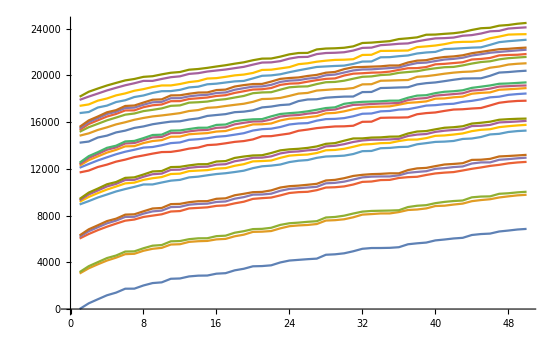

```mathematica
ListLinePlot@Array[h5GSFreq2[#, 50]&, 25]
```

Maybe this is more like it... But I don’t really see avoided crossings. Instead I just see the same pattern repeating every n steps.

We can also plot the different frequencies across the first 25 excited states. Each line is a different state (i.e. lowest is the first excitation energy, second is the second excitation, etc.)

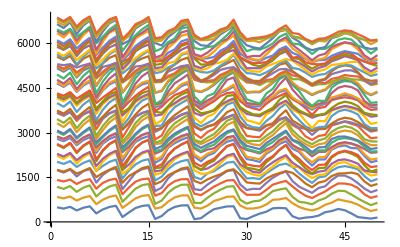

```mathematica
Array[h5Freqs2[#, 50]&, 50]//Transpose//ListLinePlot
```

Here is that in more readable form:

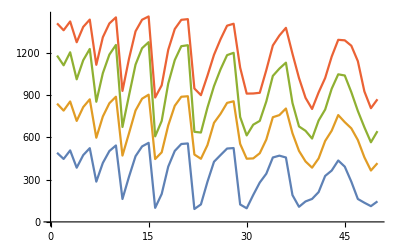

```mathematica
Array[h5Freqs2[#, 5]&, 50]//Transpose//ListLinePlot
```

#### Averaged Plots

Code

```mathematica
h5Plots2[i_, sel_:10]:=
$H5DVR[
"Wavefunctions"->h5Wfns2[i],
"Points"->{30, 30},
"WavefunctionSelection"->sel,
"ShowPotential"->False,
"WavefunctionClipping"->None,
"PlotMode"->"Density",
"PlotDisplayMode"->List,
ColorFunction->"Rainbow",
ColorFunctionScaling->True
]//Partition[#, UpTo@5]&//Grid
```

```mathematica
h5Plots3D2[i_, sel_:10]:=
$H5DVR[
"Wavefunctions"->h5Wfns2[i],
"Points"->{30, 30},
"WavefunctionSelection"->sel,
"ShowPotential"->False,
"WavefunctionClipping"->None,
"PlotMode"->"Cartesian",
"PlotDisplayMode"->List,
ColorFunction->"Rainbow",
ColorFunctionScaling->True
]//Partition[#, UpTo@5]&//Grid
```

Plots

```mathematica
h5Plots3D2[1, 3]
```

```mathematica
h5Plots3D2[7, 3]
```

```mathematica
With[{n=25, n2=5},
Map[
Sequence@@{
Prepend[Flatten@First@h5Plots2[#, n2], Row@{#, ": "}],
Join[{Null, 0}, h5Freqs2[#][[;;n2-1]]]
}&,
Ordering@Array[h5Freqs2, n][[All, 1]]
]//Grid[#/.g_Graphics:>Append[g, ImageSize->250], Dividers->{{1->Gray, -1->Gray}, Thread[Range[1, 2*n+1, 2]->Gray]}]&
]//Export["~/Documents/UW/Research/H5+/h2_outer_SA_pics.png", #]&
```

~/Documents/UW/Research/H5+/h2_outer_SA_pics.png

#### Ref

Reference states

```mathematica
#-#[[1]]&@
$H5DVR[
"Energies",
"Points"->{30, 30},
"NumberOfWavefunctions"->10
]//Rest
```

{520.322,850.812,1239.77,1388.46,1811.13,1832.47,2099.63,2287.23,2430.72}

```mathematica
$H5DVR[
"Points"->{30, 30},
"WavefunctionSelection"->10,
"ShowPotential"->False,
"WavefunctionClipping"->None,
"PlotMode"->"Density",
"PlotDisplayMode"->List,
ColorFunction->"Rainbow",
ColorFunctionScaling->True
]//Partition[#, 5]&//Grid
```

#### Transition Moments

```mathematica
h2PODVRWavefunctions=
Import@"~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns_2.mx";
```

```mathematica
rephasingData=
getPhaseCorrection[Values@h2SAWavefunctions, Keys[h2SAWavefunctions], Range[10]];
```

```mathematica
rephasedH2s2=
AssociationThread[
Keys[h2SAWavefunctions],
rephasingData["Wavefunctions"]
];
```

##### Build Base Dipole Vectors

```mathematica
hhh=Import["~/Documents/UW/Research/H5+/inputs/recentered_dipole_surface.mx"];
newInterp=
Interpolation[
Join[
Flatten[hhh["Grid"], 3],
List/@Flatten[hhh["ValuesOnGrid"], 3],
2
],
{
"ExtrapolationHandler"->{
0.&,
"WarningMessage"->False
}
}
];
h2SAInterpolatedDipoleSurface[{a_, s_}]:=
With[{R1=1/Sqrt[2.](a+s), R2=1/Sqrt[2.](s-a)},
newInterp[Sequence@@Transpose[#], R1, R2]&
]
```

```mathematica
(*h2SADipoleVectors=Import["~/Documents/UW/Research/H5+/results/h2_sa_dipole_vecs.mx"];*)
```

```mathematica
h2SADipoleVectors=
MapIndexed[
With[{fg=SelectFirst[rephasedH2s2, #=!=$Failed&]["Grid"]@"Points"},
If[#=!=$Failed,
Developer`ToPackedArray[h2SAInterpolatedDipoleSurface[#2[[1, 1]]]@fg],
$Failed
]&
],
(* This is just here for the keys and the $Failed *)
h2SAWavefunctions
];
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/h2_sa_dipole_vecs_2.mx", h2SADipoleVectors]*)
```

```mathematica
h2SADipoleVectors=Import["~/Documents/UW/Research/H5+/results/h2_sa_dipole_vecs_2.mx"];
```

```mathematica
(*h2SADipoleVectors2=
MapIndexed[
With[{fg=SelectFirst[h2PODVRWavefunctions, #=!=$Failed&]["Grid"]@"Points"},
If[#=!=$Failed,
Developer`ToPackedArray[h2SAInterpolatedDipoleSurface[#2[[1, 1]]]@fg],
$Failed
]&
],
(* This is just here for the keys and the $Failed *)
h2SAWavefunctions
];*)
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/h2_sa_po_dvr_dipole_vecs_2.mx", h2SADipoleVectors2]*)
```

~/Documents/UW/Research/H5+/results/h2_sa_po_dvr_dipole_vecs_2.mx

```mathematica
(*h2SADipoleVectors2=Import["~/Documents/UW/Research/H5+/results/h2_sa_po_dvr_dipole_vecs_2.mx"];*)
```

##### Extract Transition Moments

Calc moments

```mathematica
h2SATransitionMoments=
MapThread[
If[#=!=$Failed,
#@"TransitionMoments"[
{
#2, 
ConstantArray[0., Length[#2]], 
ConstantArray[0., Length[#2]]
},
{1, 1;;10}
],
$Failed
]&,
{
(*h2RephaseWfns*)
(*rephasedH2Wfns*)
rephasedH2s2,
h2SADipoleVectors
}
];
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/h2_t_mom_vecs.mx", h2SATransitionMoments]*)
```

~/Documents/UW/Research/H5+/results/h2_t_mom_vecs.mx

Result

```mathematica
h2SATransitionMoments=
Import["~/Documents/UW/Research/H5+/results/h2_t_mom_vecs.mx"];
```

Phase Correct These (Plots)

As always, we need to do more phase correction. Here we’ll use what we know about the symmetry of our dipole surface and functions. At -a and and +a we have:

```mathematica
notShit=Select[h2SAWavefunctions, #=!=$Failed&];
testKey=Nearest[Keys[notShit], {-1.8,2}][[1]];
testKeyInv=Nearest[Keys[notShit], {-1, 1}*testKey][[1]];
testKey2=Nearest[Keys[notShit], {-.6`,testKey[[2]]}][[1]];
testKeyInv2=Nearest[Keys[notShit], {-1, 1}*testKey2][[1]];
eqKey=Nearest[Keys[notShit], {-.0001, testKey[[2]]}][[1]];
eqKeyInv=Nearest[Keys[notShit], {.0001, testKey[[2]]}][[1]];
```

```mathematica
(*makeDipolePlots[key_]:=
With[
{
texture=
GridFunctionObject[
h2SAWavefunctions[key]["Grid"],
h2SADipoleVectors[key]
]@"Plot"["PlotMode"->"Contour", ColorFunction->"ThermometerColors", PlotRangePadding->None, Frame->False]
},
h2SAWavefunctions[key]@
"Plot"[
"PlotDisplayMode"->List, PlotStyle->Texture[texture], ImageSize->300, 
Mesh->None, ViewPoint->Above,Boxed->False, Axes->None
]
];
Grid@Transpose@
Map[makeDipolePlots, {testKey, testKey2, eqKey, testKeyInv2, testKeyInv}]*)
```

```mathematica
makeDumbPlotss[key_]:=
With[
{
wavefunctions=h2SAWavefunctions[key]["Wavefunctions"][[;;6]]
},
Map[
#@"Plot"["PlotMode"->"Density", ColorFunction->"ThermometerColors", PlotRange->All]&,
wavefunctions
]
]
makeDipoleProductPlotss[key_]:=
With[
{
dipoleFunction=
GridFunctionObject[
h2SAWavefunctions[key]["Grid"],
h2SADipoleVectors[key]
],
wavefunctions=h2SAWavefunctions[key]["Wavefunctions"][[;;6]]
},
Map[
#@"Multiply"[dipoleFunction]@"Plot"["PlotMode"->"Density", ColorFunction->"ThermometerColors", PlotRange->All]&,
wavefunctions
]
];
makeDipoleTwoProductPlotss[key_]:=
With[
{
dipoleFunction=
GridFunctionObject[
h2SAWavefunctions[key]["Grid"],
h2SADipoleVectors[key]
],
wavefunctions=h2SAWavefunctions[key]["Wavefunctions"][[;;6]]
},
Map[
#@"Multiply"[dipoleFunction]@"Multiply"[#]@"Plot"[
"PlotMode"->"Density",
 ColorFunction->ColorData[{"ThermometerColors", {-.05, .05}}], 
ColorFunctionScaling->False,
PlotRange->All
]&,
wavefunctions
]
];
```

```mathematica
(*Grid@
Riffle[
Transpose@
Map[makeDumbPlotss, {testKey, testKey2, eqKey, eqKeyInv, testKeyInv2, testKeyInv}],
Transpose@
Map[makeDipoleProductPlotss, {testKey, testKey2, eqKey, eqKeyInv, testKeyInv2, testKeyInv}]
]*)
```

```mathematica
(*Grid@Transpose@
Map[makeDipoleTwoProductPlotss, {testKey, testKey2, eqKey, testKeyInv2, testKeyInv}]*)
```

```mathematica
(*Map[makeDipoleProductPlotss, testKey]*)
```

Phase Corrected

No longer need to phase correct

```mathematica
h2SAGridTMs=
Transpose@
Map[
If[#===$Failed, ConstantArray[0., {10, 3}], #]&, 
Values@h2SATransitionMoments
];
```

Intensities

Ground state stuff

```mathematica
zaTransMoms=
zeroAveragedWavefunctions[
"TransitionMoments"[
Transpose[#],
{1, 2;;}
]
]&/@h2SAGridTMs[[;;1]];
```

Adiabatic states....

```mathematica
adiabaticStuff=
MapIndexed[
With[{wfs=#, n=#2[[1]]},
Join[
zeroAveragedWavefunctions[[;;1]],
wfs
][
"TransitionMoments"[
Transpose[#],
{1, 2;;}
]
]&/@h2SAGridTMs[[{n}]]
]&,
Join[
{
noCouplingResults2["Wavefunctions"],
noCouplingResults3["Wavefunctions"]
},
noCouplingResults456
]
]
```

Pull the GS wfn

```mathematica
zaWfn=zeroAveragedWavefunctions[[1]];
```

Get sets of projection wavefunctions to moment over

```mathematica
saTransWfns=
Map[
WavefunctionsObject[
{
Prepend[#["Energies"], zaWfn[[1]]], 
Prepend[#["Wavefunctions"], zaWfn[[2]]]
}, 
zaWfn[[2]]["Grid"]
]&,
saProjWfns
];
```

```mathematica
transWfns456=
Map[
WavefunctionsObject[
{
Prepend[#["Energies"], zaWfn[[1]]], 
Prepend[#["Wavefunctions"], zaWfn[[2]]]
}, 
zaWfn[[2]]["Grid"]
]&,
projns456
];
```

Pull transition moments and take combos

```mathematica
saTransitionMoments=
With[{wf=#},
wf@"TransitionMoments"[Transpose[#], {1, 2;;26}]&/@h2SAGridTMs
]&/@saTransWfns;
saCombos=
saTransitionMoments[[1,2,  All, 1]]+
saTransitionMoments[[2,3,  All, 1]];
```

```mathematica
transitionMoments456=
With[{wf=#},
wf@"TransitionMoments"[Transpose[#], {1, 2;;26}]&/@h2SAGridTMs
]&/@transWfns456;
combos456=
Total@MapIndexed[#[[3+#2[[1]], All, 1]]&, transitionMoments456];
```

We then turn these into intensities and plot them:

```mathematica
zaFreqs=Rest[#-#[[1]]]&@zeroAveragedWavefunctions["Energies"][[;;26]];
saFreqs=schloopWfns["Energies"]-zaWfn[[1]];
freqs456=wfns456["Energies"]-zaWfn[[1]];
```

```mathematica
adiabatic2Freqs=
noCouplingResults2["Wavefunctions"]["Energies"]-zaWfn[[1]];
adiabatic3Freqs=
noCouplingResults3["Wavefunctions"]["Energies"]-zaWfn[[1]];
adiabatic456Freqs=
Map[#["Energies"]-zaWfn[[1]]&, noCouplingResults456];
```

#### Spectra Plots

After we build the transition moments we can plot them:

```mathematica
<<ChemTools`Spectroscopy`
```

```mathematica
spec=
With[
{
freqs1=zaFreqs,
stuff1=zaFreqs*zaTransMoms[[1, All, 1]]^2,
freqs2=saFreqs[[;;25]],
stuff2=saFreqs[[;;25]]*saCombos^2,
freqs3=freqs456[[;;25]],
stuff3=freqs456[[;;25]]*combos456^2
},
ChemSpectrum[
Join[
Transpose@
{
freqs1,
stuff1/Max[Join[stuff1, stuff2, stuff3]]
},
Transpose@{
freqs2,
stuff2/Max[Join[stuff1, stuff2, stuff3]]
},
Transpose@{
freqs3,
stuff3/Max[Join[stuff1, stuff2, stuff3]]
}
]
]
]
```

ChemSpectrum[…]

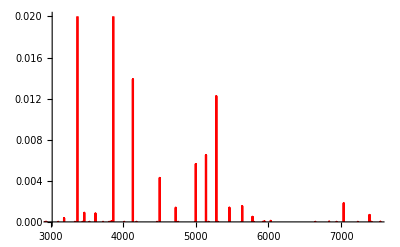

```mathematica
spec@"Plot"[PlotRange->{{3000, 7500}, {0, .02}}]
```

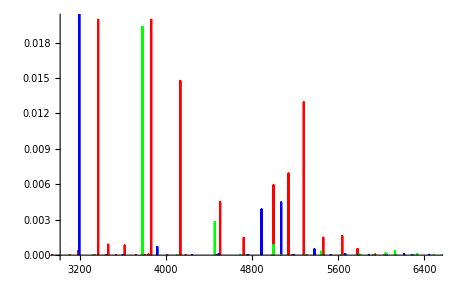

```mathematica
Show[
ChemSpectrum[…]@"Plot"[PlotRange->{{3000, 6500}, {0, .02}}, PlotStyle->Red],
specNoCouple[[2]]@"Plot"[PlotStyle->Blue],
specNoCouple[[3]]@"Plot"[PlotStyle->Green]
]
```

```mathematica
specNoCouple=
With[
{
freqs1=zaFreqs,
stuff1=zaFreqs*zaTransMoms[[1, All, 1]]^2,
freqs2=adiabatic2Freqs[[;;25]],
stuff2=adiabatic2Freqs[[;;25]]*adiabatic2[[1, All, 1]]^2,
freqs3=adiabatic3Freqs[[;;25]],
stuff3=adiabatic3Freqs[[;;25]]*adiabatic3[[1, All, 1]]^2
},
{
ChemSpectrum[
Transpose@{
freqs1,
stuff1/Max[Join[stuff1, stuff2, stuff3]]
}
],
ChemSpectrum[
Transpose@{
freqs2,
stuff2/Max[Join[stuff1, stuff2, stuff3]]
}
],
ChemSpectrum[
Transpose@{
freqs3,
stuff3/Max[Join[stuff1, stuff2, stuff3]]
}
]
}
];
```

```mathematica
specNoCouple=
With[{maxInt=Max[Map[#[[2]]&, #]]},
ChemSpectrum@Transpose[{#[[1]], #[[2]]/maxInt}]&/@#
]&@
MapThread[
With[
{
freqs1=#[[;;25]],
stuff1=#[[;;25]]*#2[[1, All, 1]]^2
},
{
freqs1,
stuff1
}
]&,
{
Join[{zaFreqs, adiabatic2Freqs, adiabatic3Freqs}, adiabatic456Freqs],
Join[{zaTransMoms, adiabatic2, adiabatic3}, adiabatic456]
}
];
```

```mathematica
specNoCouple456[[3]]@"Plot"[]
```

```mathematica
seriousPos=
Flatten@
Position[
saFreqs,
Alternatives@@spec["Window"[{3000, 6000}, {.0015, 1}]]@"Frequencies"
]
```

{1,4,5,8,12,13,15,20}

#### Fuckskakdkasdaskdaksdkasd

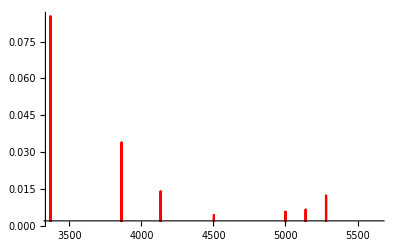

```mathematica
spec["Window"[{3000, 6000}, {.0015, 1}]]@"Plot"[]
```

```mathematica
saFreqs
```

{3370.39,3441.06,3806.31,3863.23,4133.84,4183.12,4466.24,4503.47,4723.42,4756.01,4990.3,4999.6,5139.82,5175.41,5281.35,5304.84,5461.65,5468.44,5630.78,5637.91,5780.25,5798.26,5923.6,5943.78,6030.77,6055.09,6078.52,6126.,6204.94,6219.7,6240.07,6262.71,6386.81,6413.63,6448.13,6462.99,6596.9,6620.56,6708.22,6727.86,6812.9,6839.46,6945.94,6963.97,6990.23,7000.87,7094.2,7108.85,7233.94,7251.61,7396.87,7405.01,7468.23,7492.98,7537.92,7573.04,7663.07,7680.92,7722.17,7739.46,7872.5,7875.96,7968.31,7978.19,8102.2,8112.09,8174.66,8180.08,8305.48,8305.8,8391.91,8393.04,8497.76,8498.55,8569.52,8601.72,8634.15,8650.29,8692.73,8708.39,8757.44,8761.01,8841.58,8856.06,8955.89,8976.63,8994.1,8999.7,9062.33,9073.35,9177.29,9177.5,9229.44,9248.59,9329.82,9335.84,9426.69,9428.61,9482.39,9494.4}

```mathematica
TableForm[
Transpose[
{
spec["Frequencies"][[26;;]],
Threshold[spec["Intensities"][[26;;]], .0001]
}
]
]
```

```mathematica
{
{1, 2},
{2, 1},
{2, 1|2},
{3, 2},
{3, 4},
{4, 3},
{4, 2|3},
{5, 4},
{5, 6},
{6, 5},
{6, 5|8},
{7, 6|}
```

```mathematica
schloopWfns[[;;25]]@"Plot"["PlotMode"->"Density", "PlotDisplayMode"->"List", ColorFunction->"Rainbow"]//Partition[#, 5]&//Grid
```

-Graphics-

```mathematica
saFreqs[[seriousPos]]
```

{3370.39,3863.23,4133.84,4503.47,4999.6,5139.82,5281.35,5637.91}

```mathematica
zeroAveragedWavefunctions[[;;14]]@"Plot"["PlotMode"->"Density", "PlotDisplayMode"->"List", ColorFunction->"Rainbow"
]
```

```mathematica
Show[
MatrixPlot[
Threshold[l23Coeffs[[1, seriousPos, ;;10]]^2, .001]-Threshold[l23Coeffs[[2, seriousPos, ;;10]]^2, .001],
PlotLegends->Automatic
]
]
```

```mathematica
Round[
Threshold[l23Coeffs[[1, seriousPos, ;;10]]^2, .001]-
Threshold[l23Coeffs[[2, seriousPos, ;;10]]^2, .001],
.01
]//MatrixForm
```

(0.89 | -0.08 | 0. | -0.01 | 0. | 0. | 0. | 0. | 0. | 0.
0.07 | -0.58 | 0.29 | -0.01 | 0. | 0. | 0.01 | 0.02 | 0. | 0.
0.01 | -0.28 | 0.62 | -0.06 | 0. | -0.01 | 0. | 0.01 | 0. | 0.
0.01 | 0. | 0.05 | -0.44 | 0.44 | -0.01 | 0. | 0.02 | 0. | 0.
0. | 0. | 0. | 0. | 0.02 | -0.2 | 0.62 | 0.07 | -0.02 | 0.01
0. | -0.02 | 0. | -0.02 | 0.02 | -0.4 | 0.26 | 0.19 | -0.01 | 0.01
0. | -0.01 | 0. | -0.02 | 0.01 | -0.24 | 0.01 | 0.59 | 0. | 0.04)

```mathematica
zeroAveragedWavefunctions[[;;10]]@"Plot"["PlotMode"->"Density", "PlotDisplayMode"->"List", ColorFunction->"ThermometerColors"]
```

## Equilibrium H2 Blah

```mathematica
dipoleSurf=$H5DipoleSurfaceInterps[[1]];
```

```mathematica
{minR1, minR2}={r1, r2}/.Last@NMinimize[h5PotCut[{0, Automatic, Automatic, Automatic}][{s, r1, r2}], {s, r1, r2}];
```

```mathematica
eqSurf=H5VectorizedInterpCut[{Automatic, Automatic, minR1, minR2}, dipoleSurf, 0.];
dip=eqSurf@$H5DVR["Grid"]@"Points";
dipoleVector={dip, ConstantArray[0., Length@dip], ConstantArray[0., Length@dip]};
```

```mathematica
saPot=h5PotCutVec[{Automatic, Automatic, minR1, minR2}];
saEqResults=
$H5DVR[
"PotentialFunction"->saPot,
"NumberOfWavefunctions"->25,
"PruningEnergy"->Scaled[.99]
];
```

```mathematica
saEqWfns=saEqResults["Wavefunctions"];
spec=ChemSpectrum[saEqWfns@"Intensities"[dipoleVector]];
```

```mathematica
FileNameJoin@{NotebookDirectory[],"inputs", "anne_results.csv"}
```

```mathematica
"~/Documents/UW/Research/H5+/inputs/anne_results.csv"
```

```mathematica
zhouInts=
Import["~/Documents/UW/Research/H5+/inputs/anne_results.csv"][[All, {3, -1}]];
zhouSpec=
ChemSpectrum[zhouInts];
```

```mathematica
Show[
zhouSpec@"Plot"[PlotStyle->Blue],
spec@"Plot"[]
]
```

```mathematica
Show[
zhouSpec@"Plot"[PlotRange->{0., .1}, PlotStyle->Blue],
spec@"Plot"[PlotRange->{0., .1}]
]
```

```mathematica
specTable2=Table[
{
r1,
wfs2=
$H5DVR[
"Wavefunctions",
"PotentialFunction"->h5PotCutVec[{Automatic, Automatic, r1, r2}],
"NumberOfWavefunctions"->17,
"PruningEnergy"->Scaled[.99]
];
eqSurf=H5VectorizedInterpCut[{Automatic, Automatic, r1, r2}, dipoleSurf, 0.];
spec2=
ChemSpectrum[
{
wfs2@"Frequencies"[],
wfs2@"Intensities"[
{
#,
ConstantArray[0., Length@#],
ConstantArray[0., Length@#]
}&@eqSurf@$H5DVR["Grid"]@"Points"
]
}
];
{
{Style[StringForm["r_1=``Å | r_2=``Å", 2*r1, 2*r2],FontFamily->"CMU Serif"], SpanFromLeft},
{
Show[
zhouSpec@"Plot"[PlotStyle->Blue, ImageSize->250],
spec2@"Plot"[]
],
Show[
zhouSpec@"Plot"[PlotRange->{0., .1}, PlotStyle->Blue, ImageSize->250],
spec2@"Plot"[PlotRange->{0., .1}]
]
}
}
},
{r1, .4, .5, .01},
{r2, .4, .6, .01}
];
```

```mathematica
Map[2*#[[1, 1]]->Grid@Flatten[#[[All, 2]], 1]&, specTable2]//TabView
```

```mathematica
eqH2Dist=.95/2;
eqSurf2=H5VectorizedInterpCut[{Automatic, Automatic, eqH2Dist, eqH2Dist}, dipoleSurf, 0.];
eqDipPts=eqSurf2@wfs2["Grid"]@"Points";
eqDipFunc=GridFunctionObject[wfs2["Grid"],eqDipPts];
eqDipFunc@"Plot"["PlotMode"->"Contour"]
```

```mathematica
dprods=#["Multiply"[eqDipFunc]]&/@wfs2["Wavefunctions"];
```

```mathematica
rotMat[gf_]:=
With[
{vals=dprods[[1]]@"Values"},
Rescale[
ImageData@
Echo@
ImageRotate[
Echo@Image[Rescale@vals],
-π/4, 
"Padding"->Echo@Rescale[vals[[1, 1]], MinMax[vals], {0, 1}]
],
{0, 1},
MinMax[vals]
]
]
```

```mathematica
dim=ImageData[ImageRotate[Image[Rescale@dprods[[1]]@"Values"], -π/4]];
```

```mathematica
ChemTools["Get", "Wavefunctions/Package/WavefunctionTools"]
ChemTools["Get", "Wavefunctions/WavefunctionsObject"]
```

```mathematica
dips2=
{
#,
ConstantArray[0., Length@#],
ConstantArray[0., Length@#]
}&@eqSurf@wfs2["Grid"]@"Points";
```

```mathematica
spec3=
ChemSpectrum[wfs2@"Intensities"[dips2]];
Grid@{
{Style[StringForm["r_1=``Å | r_2=``Å", 2*eqH2Dist, 2*eqH2Dist],FontFamily->"CMU Serif"], SpanFromLeft},
{
Show[
zhouSpec@"Plot"[PlotStyle->Blue, ImageSize->500],
spec3["Window"[{0, 10000}, {.000001, 1}]]@"Plot"[]
]
},
{
Show[
zhouSpec@"Plot"[PlotRange->{0., .1}, PlotStyle->Blue, ImageSize->500],
spec3["Window"[{0, 10000}, {10^-8, 1}]]@"Plot"[PlotRange->{5*10^-5, .1}]
]
}
}
```

r_1=0.95Å | r_2=0.95Å | 
-Graphics- | 
-Graphics- |

```mathematica
eqH2Dist=.95/2;
wfs2=
$H5DVR[
"Wavefunctions",
"PotentialFunction"->h5PotCutVec[{Automatic, Automatic, eqH2Dist, eqH2Dist}],
"NumberOfWavefunctions"->17,
"PruningEnergy"->Scaled[.99]
];
eqSurf2=H5VectorizedInterpCut[{Automatic, Automatic, eqH2Dist, eqH2Dist}, dipoleSurf, 0.];
spec2=
ChemSpectrum[
{
wfs2@"Frequencies"[],
wfs2@"Frequencies"[]*
wfs2@"Intensities"[
{
#,
ConstantArray[0., Length@#],
ConstantArray[0., Length@#]
}&@eqSurf@wfs2@"Points"
]
}
];
Grid@{
{Style[StringForm["r_1=``Å | r_2=``Å", 2*eqH2Dist, 2*eqH2Dist],FontFamily->"CMU Serif"], SpanFromLeft},
{
Show[
zhouSpec@"Plot"[PlotStyle->Blue, ImageSize->500],
spec2["Window"[{0, 10000}, {.000001, 1}]]@"Plot"[]
]
},
{
Show[
zhouSpec@"Plot"[PlotRange->{0., .1}, PlotStyle->Blue, ImageSize->500],
spec2["Window"[{0, 10000}, {10^-8, 1}]]@"Plot"[PlotRange->{5*10^-5, .1}]
]
}
}
```

## Old-Style 2D

```mathematica
ChemTools["Get", "DVR/Package/KineticEnergy"]
```

```mathematica
oldGrid=Import["/Users/Mark/Documents/UW/Research/H5+/archived/pot_cut.dat"];
anneGrid=
GatherBy[
QuantityMagnitude@
UnitConvert[
QuantityArray[
oldGrid[[All, {2, 1, 3}]],
{"BohrRadius", "BohrRadius", "Wavenumbers"}
],
{"Angstroms", "Angstroms", "Wavenumbers"}
],
First
];
anneInterp=Interpolation@Flatten[anneGrid, 1];
```

```mathematica
texture=
Quiet@wfnsInterp["Grid"]["BuildFunction"[anneInterp@@#&]]@"Plot"["PlotMode"->"Contour", Mesh->None , Contours->15, PlotRangePadding->None, Frame->None];
```

```mathematica
wfnsAnne=
$H5DVR[
"Points"->Dimensions[anneGrid][[;;2]],
"Range"->CoordinateBounds[anneGrid][[;;2]],
"NumberOfWavefunctions"->60,
"PotentialEnergy"->SparseArray[Band[{1, 1}]->Flatten[anneGrid, 1][[All, 3]]]
];
```

```mathematica
eqSurf2=H5VectorizedInterpCut[{Automatic, Automatic, minR1, minR2}, dipoleSurf, 0.];
dip2=eqSurf@wfnsAnne["Grid"]@"Points";
dipoleVector2={dip2, ConstantArray[0., Length@dip2], ConstantArray[0., Length@dip2]};
```

```mathematica
wfnsAnneWfns=wfnsAnne["Wavefunctions"];
specAnne=ChemSpectrum[wfnsAnneWfns@"Intensities"[dipoleVector]];
```

```mathematica
Show[
zhouSpec@"Plot"[PlotStyle->Blue],
specAnne@"Plot"[]
]
```

-Graphics-

```mathematica
Show[
specAnne@"Plot"[PlotRange->{0., .1},PlotStyle->Red,  PlotLegends->LineLegend[{Blue, Red}, {"Zhou", "Mark"}]],
zhouSpec@"Plot"[PlotRange->{0., .1}, PlotStyle->Directive[Dotted, Blue]]
]
```

-Graphics-

```mathematica
Show[
zhouSpec@"Plot"[PlotRange->{0., .1}, PlotStyle->Blue],
spec@"Plot"[PlotRange->{0., .1}]
]
```

-Graphics-

```mathematica
Show[
zhouSpec@"Plot"[PlotRange->{0., .01}, PlotStyle->Blue],
spec@"Plot"[PlotRange->{0., .01}]
]
```

-Graphics-

## Write Up